# Parameters & Configuration

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
Omm=0.3111;
Oml=1-Omm;
H0=1/2997.9;
Lp4=4;
```

```mathematica
h=0.6766
```

0.6766

## Data imput

## Covariance Integrals

```mathematica
zsigma=Import["sigma8_CAMB.dat","Table"];
```

```mathematica
varcosmicMONObare=Import["integrals/varcosmic_mono_bare.dat","Table"];
varcosmicDIPbare=Import["integrals/varcosmic_dip_bare.dat","Table"];
varcosmicQUADbare=Import["integrals/varcosmic_quad_bare.dat","Table"];
varcosmicOCTbare=Import["integrals/varcosmic_oct_bare.dat","Table"];
varcosmicHEXAbare=Import["integrals/varcosmic_hexa_bare.dat","Table"];
varcosmic02bare=Import["integrals/varcosmic_mult02_bare.dat","Table"];
varcosmic04bare=Import["integrals/varcosmic_mult04_bare.dat","Table"];
varcosmic13bare=Import["integrals/varcosmic_mult13_bare.dat","Table"];
varcosmic24bare=Import["integrals/varcosmic_mult24_bare.dat","Table"];
varmixMONObare=Import["integrals/varmix_mono_bare.dat","Table"];
varmixDIPbare=Import["integrals/varmix_dip_bare.dat","Table"];
varmixQUADbare=Import["integrals/varmix_quad_bare.dat","Table"];
varmixOCTbare=Import["integrals/varmix_oct_bare.dat","Table"];
varmixHEXAbare=Import["integrals/varmix_hexa_bare.dat","Table"];
varmix02bare=Import["integrals/varmix_mult02_bare.dat","Table"];
varmix04bare=Import["integrals/varmix_mult04_bare.dat","Table"];
varmix13bare=Import["integrals/varmix_mult13_bare.dat","Table"];
varmix24bare=Import["integrals/varmix_mult24_bare.dat","Table"];
```

## Signals Integrals

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu1_z0_fid.dat","Table"];
```

```mathematica
nu1=Interpolation[nu1baretab];
```

```mathematica
nu1z0[d_]:=d H0 nu1[d];
```

MONOPOLE

```mathematica
mu0baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu0_z0_fid.dat","Table"];
```

```mathematica
mu0=Interpolation[mu0baretab];
```

```mathematica
mu0z0[d_]:= mu0[d];
```

QUADRUPOLE

```mathematica
mu2baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu2_z0_fid.dat","Table"];
```

```mathematica
mu2=Interpolation[mu2baretab];
```

```mathematica
mu2z0[d_]:=mu2[d];
```

OCTUPOLE

```mathematica
nu1baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/nu3_z0_fid.dat","Table"];
```

```mathematica
nu3=Interpolation[nu1baretab];
```

```mathematica
nu3z0[d_]:=d H0 nu3[d];
```

HEXADECAPOLE

```mathematica
mu4baretab=Import["/Users/danielsb/Documents/GitHub/magevolbias/Signals/mu4_z0_fid.dat","Table"];
mu4=Interpolation[mu4baretab];
mu4z0[d_]:= mu4[d];
```

```mathematica
mu0Lp4zbaretab=Table[mu0z0[d],{d,4,172,4}];
nu1Lp4zbaretab=Table[nu1z0[d],{d,4,172,4}];
mu2Lp4zbaretab=Table[mu2z0[d],{d,4,172,4}];
nu3Lp4zbaretab=Table[nu3z0[d],{d,4,172,4}];
mu4Lp4zbaretab=Table[mu4z0[d],{d,4,172,4}];
```

## Cosmology

```mathematica
r[z_]:=Integrate[1/(Sqrt[Omm x^3+Oml]),{x,1,1+z}];
```

```mathematica
r[0.15]/H0
```

433.566

```mathematica
D1[z_]:=5Omm/2(Omm(1+z)^3+1-Omm)^(1/2)NIntegrate[1/(Omm/x+(1-Omm) x^2)^(3/2),{x,0,1/(1+z)}]
```

```mathematica
fz[z_]:=1/(Omm+Oml/(1+z)^3)(-3Omm/2+5Omm/2/(1+z)/D1[z]);
```

```mathematica
HH[z_]=Sqrt[Omm(1+z)+(1-Omm)/(1+z)^2];
```

```mathematica
dD1dz[z_]:=(5 Omm /2) (3 Omm (1+z)^2/(2 Sqrt[Omm (1+z)^3 + Oml]) Integrate[(1+x)/(Sqrt[Omm(1+x)^3+Oml])^3,{x,z,Infinity}] - (1+z)/(Omm(1+z)^3+Oml))
```

```mathematica
Table[{D1[0],fz[0]},{i,1}]
```

{{0.785555,0.523414}}

```mathematica
OmegaLz[z_]:=1/(Omm (1+z)^3+Oml)
```

```mathematica
OmegaMz[z_]:= Omm (1+z)^3/(Omm(1+z)^3+Oml)
```

```mathematica
zSKA=List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95]; 
(* zSKA= List[0.20,0.28,0.36,0.44,0.53,0.64,0.79, 1.03, 1.31, 1.58, 1.86]; *)
```

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
sqSKA = 30000
```

30000

```mathematica
VzSKA=ParallelTable[4/3 Pi ( r[zSKA[[i]]+0.05]^3-r[zSKA[[i]]-0.05]^3)/H0^3 sqSKA/41253,{i,1,ktot}];
fzSKA=ParallelTable[fz[zSKA[[i]]],{i,1,ktot}];
evolzSKA=ParallelTable[(D1[zSKA[[i]]]/D1[0])^2,{i,1,ktot}];
dzSKA=ParallelTable[r[zSKA[[i]]],{i,1,ktot}];
HzSKA=ParallelTable[HH[zSKA[[i]]],{i,1,ktot}];
dD1dzSKA=ParallelTable[dD1dz[zSKA[[i]]],{i,1,ktot}];
D1zSKA=Table[D1[i],{i,zSKA}];
D10=D1[0];
dfdzSKA=(3 Oml (1+zSKA)^2)/(Omm (1+zSKA)^3+Oml)^2 (-3 Omm/2 + 5 Omm /2 /((1+zSKA) D1zSKA)) - (5 Omm /2 )((1+zSKA)^3/(Omm(1+zSKA)^3+Oml))((D1zSKA+(1+zSKA) dD1dzSKA)/((1+zSKA)D1zSKA)^2);
rH0zSKA = r[zSKA];
```

```mathematica
VzSKA
```

{4.90045×10^8,1.20103×10^9,2.09836×10^9,3.09231×10^9,4.11482×10^9,5.11741×10^9,6.06784×10^9,6.94656×10^9,7.74333×10^9,8.45454×10^9,9.08098×10^9,9.62628×10^9,1.00957×10^10,1.04954×10^10,1.08317×10^10,1.11109×10^10,1.13393×10^10,1.15223×10^10,1.16654×10^10}

```mathematica
D1zSKA
```

{0.725792,0.688431,0.653295,0.620452,0.589882,0.561505,0.535207,0.510852,0.488297,0.467398,0.448017,0.430022,0.413292,0.397715,0.383189,0.369621,0.356928,0.345034,0.333872}

```mathematica
OmegaMzSKA=OmegaMz[zSKA]
```

{0.407165,0.468653,0.526309,0.579253,0.627097,0.669814,0.707623,0.740885,0.770035,0.795522,0.817786,0.837237,0.854242,0.869129,0.882186,0.893661,0.903769,0.912694,0.920593}

```mathematica
OmegaLzSKA=OmegaLz[zSKA]
```

{0.860552,0.771297,0.687605,0.610751,0.541302,0.479294,0.424412,0.376128,0.333815,0.296818,0.264499,0.236266,0.211581,0.18997,0.171017,0.15436,0.139688,0.126733,0.115266}

```mathematica
dOmegaLzSKA=- 3 Omm (1+zSKA)^2/(Omm(1+zSKA)^3+Oml)^2
```

{-0.914054,-0.86753,-0.804206,-0.731958,-0.656998,-0.583706,-0.51484,-0.451894,-0.395461,-0.345549,-0.301819,-0.263747,-0.230734,-0.202174,-0.177493,-0.156165,-0.137723,-0.121756,-0.107912}

Import CAMB results

```mathematica
Length[zsigma]
```

100

Redshift is displayed in the wrong order in zsigma. σ8 is given i

```mathematica
sigma8ztab=zsigma[[All,2]];
```

```mathematica
redshifts=zsigma[[All,1]];
```

```mathematica
zsigma8tab=Table[{redshifts[[i]],sigma8ztab[[i]]},{i,1,Length[redshifts]}];
```

```mathematica
sigma8z=Interpolation[zsigma8tab];
```

```mathematica
Sigma8z0=sigma8z[0]
```

0.814468

```mathematica
sigma8z[0]*D1[0.5]/D1[0]
```

0.627151

```mathematica
sigma8z[0.5]
```

0.627168

```mathematica
Sigma8zSKA=sigma8z[zSKA];
```

# Magnification & Evolution Bias

### Population parameters

```mathematica
b1=0.554;
b2=0.783;
bmeanzSKA=b1 Exp[b2 zSKA];
```

```mathematica
bB[m_, dbz_]:=bmeanzSKA+(m-1)dbz/m ;
bF[m_, dbz_]:=bmeanzSKA-dbz/m;
bTzSKA:=bmeanzSKA ;
```

### Standard splitting 50% (m = 2)

```mathematica
m = 2;
```

```mathematica
db=1.0;
dbz=Table[db,{i,Length[zSKA]}];
```

#### Bright

```mathematica
nBSKA = 1/2;
```

```mathematica
smodelBzSKA = List[0.22441708,0.35788955,0.47077869,0.54038551,0.60761985,0.67991981,0.7531311,0.81864417,0.88081715,0.94857743,1.02785004,1.12008456,1.21930805,1.32187692,1.42534363,1.52897325,1.63180455,1.73334715,1.83420913];
```

```mathematica
fevolBzSKA = List[3.00956639,0.07976877,-0.81552783,-0.6173486,-0.39242556,-0.31155665,-0.26595514,-0.1091582,0.07791229,0.18253319,0.17336397,0.03980399,-0.12308668,-0.28681099,-0.41997146,-0.51728093,-0.57341237,-0.57764042,-0.55234844];
```

```mathematica
bBzSKA = bB[m, dbz]
```

{1.12304,1.17379,1.22867,1.28801,1.35219,1.4216,1.49666,1.57784,1.66563,1.76056,1.86323,1.97426,2.09434,2.22419,2.36462,2.51649,2.68073,2.85834,3.05042}

#### Faint

```mathematica
nFSKA = 1/2;
```

```mathematica
smodelzSKA = List[0.10126775,0.16794581,0.24591785,0.34042118,0.44359672,0.54749941,0.64724732,0.74425817,0.83940737,0.93348225,1.02841809,1.12429914,1.2228487,1.3231631,1.42622787,1.53202081,1.64045919,1.75174659,1.86291714];
```

```mathematica
(*Check if'm' exists and if it's equal to a desired value*)
If[!ValueQ[m]||m!=2,m=1/(1-nFSKA);]
```

```mathematica
m
```

2

```mathematica
smodelFzSKA = (m/(m-1)) smodelzSKA -(1/(m-1)) smodelBzSKA
```

{-0.0218816,-0.0219979,0.021057,0.140457,0.279574,0.415079,0.541364,0.669872,0.797998,0.918387,1.02899,1.12851,1.22639,1.32445,1.42711,1.53507,1.64911,1.77015,1.89163}

```mathematica
fevolFzSKA =List[1.49669846,4.74321837,4.48561914,3.00325909,1.42466759,0.23953114,-0.63019961,-1.38888192,-2.01572455,-2.47043394,-2.7319998,-2.83059041,-2.87381247,-2.89939059,-2.94565432,-3.01777315,-3.12068025,-3.25274921,-3.36209773];
```

```mathematica
bFzSKA= bF[m, dbz]
```

{0.123042,0.173787,0.228665,0.288013,0.352194,0.421603,0.496665,0.57784,0.665627,0.760564,0.863233,0.974265,1.09434,1.22419,1.36462,1.51649,1.68073,1.85834,2.05042}

# Covariance

## Parameters

```mathematica
Redshift = List[0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95];
```

```mathematica
RedshifteBOSS = List[0.65,0.75,0.85,0.95];
```

```mathematica
NbarzSKAlist=List[6.2 10^-2/h^3,3.63 10^-2/h^3,2.16 10^-2/h^3,1.31 10^-2/h^3,8.07 10^-3/h^3,5.11 10^-3/h^3,3.27 10^-3/h^3,2.11 10^-3/h^3,1.36 10^-3/h^3,8.7 10^-4/h^3,5.56 10^-4/h^3,3.53 10^-4/h^3,2.22 10^-4/h^3,1.39 10^-4/h^3,8.55 10^-5/h^3,5.2 10^-5/h^3,3.12 10^-5/h^3,1.83 10^-5/h^3,1.05 10^-5/h^3];
Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]
```

{{0.15,0.200168},{0.25,0.117195},{0.35,0.0697361},{0.45,0.0422937},{0.55,0.0260542},{0.65,0.0164978},{0.75,0.0105573},{0.85,0.00681219},{0.95,0.00439079},{1.05,0.00280882},{1.15,0.00179506},{1.25,0.00113967},{1.35,0.000716732},{1.45,0.000448765},{1.55,0.000276039},{1.65,0.000167883},{1.75,0.00010073},{1.85,0.000059082},{1.95,0.0000338995}}

```mathematica
NbarzSKAfint= Interpolation[Table[{Redshift[[i]], NbarzSKAlist[[i]]}, {i,1,Length[NbarzSKAlist]}]];
NbarzSKA = NbarzSKAfint[zSKA]
```

{0.200168,0.117195,0.0697361,0.0422937,0.0260542,0.0164978,0.0105573,0.00681219,0.00439079,0.00280882,0.00179506,0.00113967,0.000716732,0.000448765,0.000276039,0.000167883,0.00010073,0.000059082,0.0000338995}

```mathematica
NbareBOSS = NbarzSKAfint[RedshifteBOSS]
```

{0.0164978,0.0105573,0.00681219,0.00439079}

```mathematica
NtotSKA=Sum[NbarzSKA[[k]]VzSKA[[k]],{k,1,Length[zSKA]}]
```

9.23016×10^8

```mathematica
sqeBOSS = 10000
```

10000

```mathematica
VzeBOSS=ParallelTable[4/3 Pi ( r[RedshifteBOSS[[i]]+0.05]^3-r[RedshifteBOSS[[i]]-0.05]^3)/H0^3 sqeBOSS/41253,{i,1,Length[RedshifteBOSS]}]
```

{1.7058×10^9,2.02261×10^9,2.31552×10^9,2.58111×10^9}

```mathematica
NtoteBOSS = Sum[NbareBOSS[[k]]VzeBOSS[[k]],{k,1,Length[RedshifteBOSS]}]
```

7.66021×10^7

```mathematica
(*nBSKA=1/m;*)
(*nFSKA=1-nBSKA;*)
nBzSKA=Table[nBSKA, {i,Length[zSKA]}];
nFzSKA=Table[nFSKA, {i,Length[zSKA]}];
```

```mathematica
nBzSKA
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
nFzSKA
```

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
NbarBzSKA=NbarzSKA*nBzSKA
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

```mathematica
NbarFzSKA=NbarzSKA*nFzSKA
```

{0.100084,0.0585977,0.0348681,0.0211468,0.0130271,0.00824888,0.00527864,0.00340609,0.0021954,0.00140441,0.00089753,0.000569834,0.000358366,0.000224382,0.000138019,0.0000839416,0.000050365,0.000029541,0.0000169498}

Coefficient for the mixed terms

```mathematica
coeff2popSKA=(evolzSKA/(VzSKA*NbarzSKA))
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffFSKA=evolzSKA/(VzSKA*NbarzSKA)
```

{8.70241×10^-9,5.45636×10^-9,4.72637×10^-9,4.76986×10^-9,5.25955×10^-9,6.05173×10^-9,7.2461×10^-9,8.93679×10^-9,1.13643×10^-8,1.49076×10^-8,1.99537×10^-8,2.73143×10^-8,3.82531×10^-8,5.44219×10^-8,7.95805×10^-8,1.18687×10^-7,1.80744×10^-7,2.83384×10^-7,4.56788×10^-7}

```mathematica
coeffBSKA /nBzSKA
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

```mathematica
coeffFSKA/nFzSKA
```

{1.74048×10^-8,1.09127×10^-8,9.45275×10^-9,9.53971×10^-9,1.05191×10^-8,1.21035×10^-8,1.44922×10^-8,1.78736×10^-8,2.27287×10^-8,2.98152×10^-8,3.99075×10^-8,5.46287×10^-8,7.65062×10^-8,1.08844×10^-7,1.59161×10^-7,2.37373×10^-7,3.61488×10^-7,5.66768×10^-7,9.13575×10^-7}

Coefficients for the Cosmic Variance

```mathematica
coeffCCSKA=evolzSKA^2/VzSKA
```

{1.48698×10^-9,4.91113×10^-10,2.27956×10^-10,1.25847×10^-10,7.72686×10^-11,5.10105×10^-11,3.55097×10^-11,2.57457×10^-11,1.92798×10^-11,1.48236×10^-11,1.16503×10^-11,9.3282×10^-12,7.589×10^-12,6.26012×10^-12,5.22696×10^-12,4.41133×10^-12,3.75864×10^-12,3.23×10^-12,2.79714×10^-12}

SET FEVOL =  0 MANUALLY

```mathematica
(*fevolBzSKA = Table[0.,{i,1,ktot}];
fevolFzSKA = Table[0.,{i,1,ktot}];*)
```

Coefficients needed for the cosmic variance of the dipole from relativistic effects

```mathematica
cBzSKA=(5smodelBzSKA +(2-5smodelBzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2-fevolBzSKA)fzSKA
```

{3.03044,1.96942,1.50533,1.08587,0.778835,0.633417,0.577577,0.500896,0.433983,0.449219,0.574176,0.83023,1.14574,1.49666,1.85103,2.19899,2.5307,2.83137,3.11887}

```mathematica
cFzSKA=(5smodelFzSKA +(2-5smodelFzSKA)/(dzSKA HzSKA)+1/2(-Omm(1+zSKA)+2/(1+zSKA)^2(1-Omm))/HzSKA^2- fevolFzSKA)fzSKA
```

{8.73219,3.49283,1.72274,1.11051,1.14024,1.34369,1.62634,2.0112,2.43762,2.84422,3.1753,3.42655,3.6648,3.91551,4.20934,4.55135,4.94709,5.39644,5.84627}

```mathematica
indist=5;
Acc =1.0 ;
```

```mathematica
distances=Table[d,{d,4,172,4}]
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
Table[distances[[d]],{d,indist,Length[distances]}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172}

```mathematica
maxsep=Length[distances]-3
```

40

```mathematica
dists =Table[distances[[d]],{d,indist,maxsep}]
```

{20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160}

```mathematica
dtot =Length[dists]
```

36

```mathematica
ldist=maxsep-(indist-1)
```

36

```mathematica
8 ldist
```

288

```mathematica
ktot=Length[zSKA]
```

19

```mathematica
dmin =distances[[indist]];
dmax =  distances[[maxsep]];
```

```mathematica
{dmin, dmax}
```

{20,160}

## Multipole’s Coefficients

### Cosmic Variance

#### Definitions

```mathematica
G[n_,m_,a_,b_]:=Integrate[LegendreP[n,x]LegendreP[m,x]LegendreP[a,x]LegendreP[b,x],{x,-1,1}]
```

```mathematica
alpha0[bL_,bM_,f_]:=bL bM +(bL+bM)/3 f+f^2/5
alpha2[bL_,bM_,f_]:=2/3(bL+bM) f+4f^2/7
alpha4[bL_,bM_,f_]:=8f^2/35
```

```mathematica
coeffvarianceCC[n_,m_,bL_,bM_,bN_,bP_,f_]:=
Collect[
1/4((alpha0[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha0[bM, bN,f])G[n,m,0,0]+(alpha0[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha2[bM, bN,f])G[n,m,0,2]+(alpha0[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha0[bL, bP,f]alpha4[bM, bN,f])G[n,m,0,4]+(alpha2[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha0[bM, bN,f])G[n,m,2,0]+(alpha2[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha2[bM, bN,f])G[n,m,2,2]+(alpha2[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha2[bL, bP,f]alpha4[bM, bN,f])G[n,m,2,4]+(alpha4[bL, bN,f]alpha0[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha0[bM, bN,f])G[n,m,4,0]+(alpha4[bL, bN,f]alpha2[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha2[bM, bN,f])G[n,m,4,2]+(alpha4[bL, bN,f]alpha4[bM, bP,f]+(-1)^m alpha4[bL, bP,f]alpha4[bM, bN,f])G[n,m,4,4]),f,Simplify]
```

```mathematica
corrCC[n_,m_]:=If[n==m,1,(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCC[n_,m_,bL_,bM_,bN_,bP_,f_]:= corrCC[n,m]coeffvarianceCC[n,m,bL,bM,bN,bP,f]
```

COSMIC VARIANCE (DIPOLE)

```mathematica
alpha1[bL_,bM_,cL_,cM_,f_]:=cL(bM+3f/5)-cM(bL+3f/5)
alpha3[bL_,bM_,cL_,cM_,f_]:=2f/5(cL-cM)
```

```mathematica
coeffcovCCrel[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=corrCC[n,m]Collect[(alpha1[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,1,1]+alpha1[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,1,3]+alpha3[bL, bM,cL,cM,f]alpha1[bN, bP,cN,cP,f]G[n,m,3,1]+alpha3[bL, bM,cL,cM,f]alpha3[bN, bP,cN,cP,f]G[n,m,3,3]),f,Simplify]
```

```mathematica
coeffvarCCrelSKAz[n_,m_,bL_,bM_,bN_,bP_,cL_,cM_,cN_,cP_,f_]:=evolzSKA^2 /VzSKA /4HzSKA^2coeffcovCCrel[n,m,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

```mathematica
varcosmicMONOzbaretab=Table[varcosmicMONObare,{i,Length[zSKA]}];
```

```mathematica
coeffvarianceCC[1,1,bL,bM,bL,bM,f]
```

0

```mathematica
coeffcovCCrel[1,1,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

2/5 (bM cL-bL cM)^2+4/7 (cL-cM) (bM cL-bL cM) f+2/9 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[3,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

46/315 (bM cL-bL cM)^2+52/231 (cL-cM) (bM cL-bL cM) f+14/143 (cL-cM)^2 f^2

```mathematica
coeffcovCCrel[1,3,bL,bM,bL,bM,cL,cM,cL,cM,f]
```

-21 (4/35 (bM cL-bL cM)^2+16/63 (cL-cM) (bM cL-bL cM) f+4/33 (cL-cM)^2 f^2)

```mathematica
corrCC[3,3]
```

1

```mathematica
corrCC[1,3]
```

-21

```mathematica
corrCC[1,3]coeffcovCCrel[1,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

441 (4/35 (bM cL-bL cM) (bP cN-bN cP)-8/63 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+4/33 (cL-cM) (cN-cP) f^2)

From 4 to 172 Mpc/h

```mathematica
varcosmicMONObare[[5,1]]
```

4.

```mathematica
varcosmicMONObare[[4,2]]
```

4.

```mathematica
varcosmicMONObare[[47,1]]
```

172.

```mathematica
varcosmicMONObare[[4,44]]
```

172.

```mathematica
4 i /. i-> 1
```

4

```mathematica
4 i /. i -> 43
```

172

```mathematica
varcosmicQUADzbaretab=Table[varcosmicQUADbare,{i,Length[zSKA]}];
```

```mathematica
varcosmicHEXAzbaretab=Table[varcosmicHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varcosmic02zbaretab=Table[varcosmic02bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic04zbaretab=Table[varcosmic04bare,{i,Length[zSKA]}];
```

```mathematica
varcosmic24zbaretab=Table[varcosmic24bare,{i,Length[zSKA]}];
varcosmicDIPzbaretab=Table[varcosmicDIPbare, {i,Length[zSKA]}];
varcosmicOCTzbaretab=Table[varcosmicOCTbare, {i,Length[zSKA]}];
varcosmic13zbaretab=Table[varcosmic13bare, {i,Length[zSKA]}];
```

#### Monopole

```mathematica
coeffvarCC00=coeffvarCC[0,0,bL,bM,bN,bP,f]
```

bL bM bN bP+1/3 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+1/5 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+1/7 (bL+bM+bN+bP) f^3+f^4/9

Monopole - 1 Population

```mathematica
coeffvarCC[0,0,B,B,B,B,f]
```

B^4+(4 B^3 f)/3+(6 B^2 f^2)/5+(4 B f^3)/7+f^4/9

```mathematica
coeffvarCC1pop00BzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{5.14716×10^-9,2.0861×10^-9,1.18089×10^-9,7.91299×10^-10,5.87812×10^-10,4.68678×10^-10,3.93883×10^-10,3.45035×10^-10,3.12722×10^-10,2.91753×10^-10,2.79124×10^-10,2.73059×10^-10,2.72527×10^-10,2.76985×10^-10,2.86237×10^-10,3.00367×10^-10,3.19696×10^-10,3.44781×10^-10,3.76425×10^-10}

```mathematica
coeffvarCC1pop00FzSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{5.88914×10^-11,3.46207×10^-11,2.67228×10^-11,2.33396×10^-11,2.18555×10^-11,2.14219×10^-11,2.17109×10^-11,2.25943×10^-11,2.40389×10^-11,2.60678×10^-11,2.87455×10^-11,3.2174×10^-11,3.64944×10^-11,4.18928×10^-11,4.86096×10^-11,5.69514×10^-11,6.73087×10^-11,8.01769×10^-11,9.61851×10^-11}

```mathematica
varCCMONOBrightLp4d4to172zSKA=Table[coeffvarCC1pop00BzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOFaintLp4d4to172zSKA=Table[coeffvarCC1pop00FzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47},{j,2,44}];
```

```mathematica
coeffvarCC1pop00BFzSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.76087×10^-10,2.38698×10^-10,1.61179×10^-10,1.25453×10^-10,1.0613×10^-10,9.49378×10^-11,8.84867×10^-11,8.5185×10^-11,8.42264×10^-11,8.52006×10^-11,8.79231×10^-11,9.23563×10^-11,9.85728×10^-11,1.0674×10^-10,1.17119×10^-10,1.3007×10^-10,1.46066×10^-10,1.65718×10^-10,1.89802×10^-10}

```mathematica
varCCMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCC1pop00BFzSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations

```mathematica
coeffvarCC[0,0,B,F,B,F,f]
```

f^4/9+B^2 F^2+2/7 f^3 (B+F)+2/3 B f F (B+F)+1/5 f^2 (B^2+4 B F+F^2)

```mathematica
coeffvarCC2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.76087×10^-10,2.38698×10^-10,1.61179×10^-10,1.25453×10^-10,1.0613×10^-10,9.49378×10^-11,8.84867×10^-11,8.5185×10^-11,8.42264×10^-11,8.52006×10^-11,8.79231×10^-11,9.23563×10^-11,9.85728×10^-11,1.0674×10^-10,1.17119×10^-10,1.3007×10^-10,1.46066×10^-10,1.65718×10^-10,1.89802×10^-10}

```mathematica
varCCMONO2popLp4d4to172zSKA=Table[coeffvarCC2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole 1 pop - Monopole 2 pop

```mathematica
coeffvarCCBright2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.47991×10^-9,6.76238×10^-10,4.22143×10^-10,3.07057×10^-10,2.44745×10^-10,2.07574×10^-10,1.84327×10^-10,1.69719×10^-10,1.61004×10^-10,1.56673×10^-10,1.55884×10^-10,1.5819×10^-10,1.63407×10^-10,1.71542×10^-10,1.82762×10^-10,1.9738×10^-10,2.15861×10^-10,2.38835×10^-10,2.67126×10^-10}

```mathematica
coeffvarCCFaint2pop00zSKA=coeffCCSKA coeffvarCC[0,0,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.63989×10^-10,8.92101×10^-11,6.45389×10^-11,5.33212×10^-11,4.75504×10^-11,4.46054×10^-11,4.34247×10^-11,4.35299×10^-11,4.47057×10^-11,4.68768×10^-11,5.00556×10^-11,5.43209×10^-11,5.98106×10^-11,6.67226×10^-11,7.53215×10^-11,8.59508×10^-11,9.90494×10^-11,1.15174×10^-10,1.35031×10^-10}

```mathematica
varCCMONOBrigth2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k] ]varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCMONOFaint2popLp4d4to172zSKA= Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole

```mathematica
coeffvarCC[1,1,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,1,B,F,B,F,cB,cF,cB,cF,f]
```

2/9 (cB-cF)^2 f^2+2/5 (B cF-cB F)^2+4/7 (cB-cF) f (-B cF+cB F)

```mathematica
coeffvarCC11relzSKA=coeffvarCCrelSKAz[1,1,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{1.86149×10^-8,8.17618×10^-10,6.44169×10^-11,1.25285×10^-11,1.28138×10^-11,1.64922×10^-11,2.10104×10^-11,2.90179×10^-11,3.83582×10^-11,4.55576×10^-11,4.80671×10^-11,4.57049×10^-11,4.24801×10^-11,3.95744×10^-11,3.81806×10^-11,3.83713×10^-11,4.03762×10^-11,4.45655×10^-11,4.94165×10^-11}

```mathematica
varCCDIPrelLp4d4to172zSKA=Table[coeffvarCC11relzSKA[[k]] varcosmicDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

2/5 (bM cL-bL cM) (bP cN-bN cP)-2/7 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+2/9 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[1,1,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[1,1,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

#### Quadrupole

```mathematica
coeffvarCC[2,2,B,B,B,B,f]
```

B^4/5+(44 B^3 f)/105+(18 B^2 f^2)/35+(68 B f^3)/231+(83 f^4)/1287

Cuadrupole - 1 Population

```mathematica
coeffvarCC1pop22BzSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{1.49198×10^-9,6.10956×10^-10,3.47834×10^-10,2.33506×10^-10,1.73208×10^-10,1.37529×10^-10,1.14843×10^-10,9.97751×10^-11,8.95568×10^-11,8.2647×10^-11,7.81418×10^-11,7.5495×10^-11,7.43758×10^-11,7.45928×10^-11,7.60519×10^-11,7.87329×10^-11,8.26777×10^-11,8.79851×10^-11,9.48117×10^-11}

```mathematica
coeffvarCC1pop22FzSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{3.03935×10^-11,1.72406×10^-11,1.28486×10^-11,1.08337×10^-11,9.78899×10^-12,9.25244×10^-12,9.03719×10^-12,9.05975×10^-12,9.28331×10^-12,9.69607×10^-12,1.03021×10^-11,1.11177×10^-11,1.21702×10^-11,1.34984×10^-11,1.51539×10^-11,1.72038×10^-11,1.97335×10^-11,2.28519×10^-11,2.66965×10^-11}

```mathematica
varCCQUADBrightLp4d4to172zSKA= Table[coeffvarCC1pop22BzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaintLp4d4to172zSKA= Table[coeffvarCC1pop22FzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC1pop22BFzSKA = coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{1.9946×10^-10,9.70881×10^-11,6.37533×10^-11,4.82884×10^-11,3.97588×10^-11,3.4613×10^-11,3.13937×10^-11,2.94086×10^-11,2.8297×10^-11,2.7862×10^-11,2.79968×10^-11,2.86504×10^-11,2.98097×10^-11,3.14915×10^-11,3.37385×10^-11,3.6619×10^-11,4.02288×10^-11,4.46948×10^-11,5.01808×10^-11}

```mathematica
varCCQUADBrightFaintLp4d4to172zSKA = Table[coeffvarCC1pop22BFzSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole - 2 populations

```mathematica
coeffvarCC2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.9946×10^-10,9.70881×10^-11,6.37533×10^-11,4.82884×10^-11,3.97588×10^-11,3.4613×10^-11,3.13937×10^-11,2.94086×10^-11,2.8297×10^-11,2.7862×10^-11,2.79968×10^-11,2.86504×10^-11,2.98097×10^-11,3.14915×10^-11,3.37385×10^-11,3.6619×10^-11,4.02288×10^-11,4.46948×10^-11,5.01808×10^-11}

```mathematica
varCCQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop22zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{5.28048×10^-10,2.3746×10^-10,1.4595×10^-10,1.0448×10^-10,8.18991×10^-11,6.82553×10^-11,5.95159×10^-11,5.37767×10^-11,5.00416×10^-11,4.77528×10^-11,4.65869×10^-11,4.63569×10^-11,4.69625×10^-11,4.8364×10^-11,5.05681×10^-11,5.36215×10^-11,5.76091×10^-11,6.26556×10^-11,6.89296×10^-11}

```mathematica
coeffvarCCFaint2pop22zSKA=coeffCCSKA coeffvarCC[2,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.73861×10^-11,4.06653×10^-11,2.84528×10^-11,2.27446×10^-11,1.96249×10^-11,1.7809×10^-11,1.67692×10^-11,1.62576×10^-11,1.615×10^-11,1.63848×10^-11,1.69368×10^-11,1.78055×10^-11,1.90091×10^-11,2.0583×10^-11,2.25797×10^-11,2.50706×10^-11,2.8149×10^-11,3.19344×10^-11,3.65789×10^-11}

```mathematica
varCCQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop00zSKA[[k]] varcosmicQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

```mathematica
coeffvarCC[3,3,b,b,b,b,f]
```

0

```mathematica
coeffcovCCrel[3,3,B,F,B,F,cB,cF,cB,cF,f]
```

14/143 (cB-cF)^2 f^2+46/315 (B cF-cB F)^2+52/231 (cB-cF) f (-B cF+cB F)

```mathematica
coeffCCSKA coeffvarCC[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{7.09364×10^-27,6.22985×10^-27,2.10078×10^-27,2.59244×10^-27,-1.20636×10^-27,-1.22779×10^-27,-1.43989×10^-27,2.16051×10^-27,-1.45486×10^-27,2.49433×10^-27,-1.47534×10^-27,2.35446×10^-27,-1.05319×10^-27,-1.47419×10^-27,-3.2189×10^-28,-2.83905×10^-27,-5.22594×10^-27,-2.99488×10^-27,-2.65419×10^-27}

```mathematica
coeffvarCC33relzSKA=coeffvarCCrelSKAz[3,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{7.03832×10^-9,3.06549×10^-10,2.37381×10^-11,4.58227×10^-12,4.7844×10^-12,6.22522×10^-12,7.96658×10^-12,1.10363×10^-11,1.4606×10^-11,1.73378×10^-11,1.82615×10^-11,1.73186×10^-11,1.60515×10^-11,1.49121×10^-11,1.43515×10^-11,1.43934×10^-11,1.51207×10^-11,1.66691×10^-11,1.84632×10^-11}

```mathematica
varCCOCTrelLp4d4to172zSKA=Table[coeffvarCC33relzSKA[[k]] varcosmicOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f]
```

46/315 (bM cL-bL cM) (bP cN-bN cP)-26/231 (bL cM cN+bP (-cL+cM) cN+bN cL cP-bL cM cP-bN cM cP+bM cL (-cN+cP)) f+14/143 (cL-cM) (cN-cP) f^2

```mathematica
Simplify[Collect[coeffcovCCrel[3,3,bN,bP,bL,bM,cN,cP,cL,cM,f]-coeffcovCCrel[3,3,bL,bM,bN,bP,cL,cM,cN,cP,f],f]]
```

0

```mathematica
Diagonal[varCCOCTrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.26952×10^-12,1.15851×10^-11,3.69807×10^-11,7.84976×10^-11,1.34481×10^-10,2.02227×10^-10,2.78815×10^-10,3.61511×10^-10,4.47942×10^-10,5.36159×10^-10,6.24796×10^-10,7.13116×10^-10,7.99851×10^-10,8.83167×10^-10,9.59649×10^-10}

```mathematica
Diagonal[varCCDIPrelLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.37834×10^-10,7.48689×10^-10,1.33666×10^-9,1.90965×10^-9,2.42757×10^-9,2.87585×10^-9,3.25248×10^-9,3.56144×10^-9,3.80943×10^-9,4.00419×10^-9,4.15382×10^-9,4.26666×10^-9,4.35101×10^-9,4.41372×10^-9,4.45871×10^-9}

```mathematica
Diagonal[varCCQUADBrightLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{2.64397×10^-6,5.73786×10^-6,7.85923×10^-6,9.12836×10^-6,9.78663×10^-6,0.0000100305,0.0000100009,9.79555×10^-6,9.48189×10^-6,9.10991×10^-6,8.71551×10^-6,8.31572×10^-6,7.88068×10^-6,7.38295×10^-6,6.86069×10^-6}

#### Hexadecapole

```mathematica
coeffvarCC44=coeffvarCC[4,4,bL,bM,bN,bP,f]
```

1/9 bL bM bN bP+13/231 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(643 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/15015+(109 (bL+bM+bN+bP) f^3)/3003+(79 f^4)/2431

Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop44=coeffvarCC[4,4,B,B,B,B,f]
```

B^4/9+(52 B^3 f)/231+(1286 B^2 f^2)/5005+(436 B f^3)/3003+(79 f^4)/2431

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCCtotpop44zSKA= coeffCCSKA coeffvarCC[4,4,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.66145×10^-10,7.50824×10^-11,4.65919×10^-11,3.37633×10^-11,2.68328×10^-11,2.26944×10^-11,2.00951×10^-11,1.84471×10^-11,1.74459×10^-11,1.69242×10^-11,1.67885×10^-11,1.69889×10^-11,1.75044×10^-11,1.83346×10^-11,1.94968×10^-11,2.10241×10^-11,2.2966×10^-11,2.53903×10^-11,2.83856×10^-11}

```mathematica
varCCHEXAtotpopLp4d4to172zSKA=Table[coeffvarCCtotpop44zSKA[[k]] varcosmicHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCC[0,2,B,B,B,B,f]
```

-5 ((8 B^3 f)/15+(24 B^2 f^2)/35+(8 B f^3)/21+(8 f^4)/99)

```mathematica
coeffvarCC1pop02BzSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-6.60289×10^-9,-2.75171×10^-9,-1.58147×10^-9,-1.06481×10^-9,-7.87998×10^-10,-6.2142×10^-10,-5.13377×10^-10,-4.39729×10^-10,-3.87894×10^-10,-3.5076×10^-10,-3.24061×10^-10,-3.05116×10^-10,-2.92193×10^-10,-2.84152×10^-10,-2.80244×10^-10,-2.79989×10^-10,-2.83103×10^-10,-2.89454×10^-10,-2.99032×10^-10}

```mathematica
coeffvarCC1pop02FzSKA=coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.94281×10^-10,-1.10325×10^-10,-8.21029×10^-11,-6.89552×10^-11,-6.18963×10^-11,-5.79539×10^-11,-5.59025×10^-11,-5.51656×10^-11,-5.54527×10^-11,-5.66164×10^-11,-5.8591×10^-11,-6.13625×10^-11,-6.49544×10^-11,-6.94212×10^-11,-7.48451×10^-11,-8.13364×10^-11,-8.90348×10^-11,-9.81126×10^-11,-1.08779×10^-10}

```mathematica
varCCMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCC1pop02BzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaintLp4d4to172zSKA=Table[coeffvarCC1pop02FzSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCC02BrightFaint=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.26462×10^-9,-6.06515×10^-10,-3.92107×10^-10,-2.92062×10^-10,-2.3613×10^-10,-2.01497×10^-10,-1.78778×10^-10,-1.63472×10^-10,-1.5318×10^-10,-1.46532×10^-10,-1.42701×10^-10,-1.41182×10^-10,-1.4167×10^-10,-1.4399×10^-10,-1.48066×10^-10,-1.53896×10^-10,-1.61541×10^-10,-1.71118×10^-10,-1.82801×10^-10}

```mathematica
varCCMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCC02BrightFaint[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole/Cuadrupole - 2 populations

```mathematica
coeffvarCC[0,2,B,F,B,F,f]
```

-5 ((8 f^4)/99+4/21 f^3 (B+F)+4/15 B f F (B+F)+4/35 f^2 (B^2+4 B F+F^2))

```mathematica
coeffvarCC2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.26462×10^-9,-6.06515×10^-10,-3.92107×10^-10,-2.92062×10^-10,-2.3613×10^-10,-2.01497×10^-10,-1.78778×10^-10,-1.63472×10^-10,-1.5318×10^-10,-1.46532×10^-10,-1.42701×10^-10,-1.41182×10^-10,-1.4167×10^-10,-1.4399×10^-10,-1.48066×10^-10,-1.53896×10^-10,-1.61541×10^-10,-1.71118×10^-10,-1.82801×10^-10}

```mathematica
varCCMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCC2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCCBright2pop02zSKA=coeffCCSKA coeffvarCC[0,2,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-3.0985×10^-9,-1.36518×10^-9,-8.23495×10^-10,-5.78658×10^-10,-4.44924×10^-10,-3.63263×10^-10,-3.09819×10^-10,-2.73324×10^-10,-2.47844×10^-10,-2.29997×10^-10,-2.17746×10^-10,-2.09813×10^-10,-2.05384×10^-10,-2.03939×10^-10,-2.05159×10^-10,-2.08868×10^-10,-2.15004×10^-10,-2.23595×10^-10,-2.34749×10^-10}

```mathematica
coeffvarCCFaint2pop02zSKA= coeffCCSKA coeffvarCC[0,2,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-4.97725×10^-10,-2.60099×10^-10,-1.8056×10^-10,-1.42878×10^-10,-1.21744×10^-10,-1.08827×10^-10,-1.00668×10^-10,-9.56067×10^-11,-9.27634×10^-11,-9.16448×10^-11,-9.19686×10^-11,-9.35799×10^-11,-9.64071×10^-11,-1.00439×10^-10,-1.05713×10^-10,-1.12307×10^-10,-1.20341×10^-10,-1.29973×10^-10,-1.41405×10^-10}

```mathematica
varCCMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCCBright2pop02zSKA[[k]] varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCCFaint2pop02zSKA[[k]]  varcosmic02zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[0,4,bL,bM,bN,bP,f]
```

9 (8/315 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2+8/231 (bL+bM+bN+bP) f^3+(16 f^4)/429)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,B,T,T,f]
```

9 ((16 f^4)/429+16/231 f^3 (B+T)+8/315 f^2 (B^2+4 B T+T^2))

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCC1pop04BzSKA= coeffCCSKA coeffvarCC[0,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{9.94159×10^-10,4.35712×10^-10,2.59554×10^-10,1.78996×10^-10,1.34347×10^-10,1.06575×10^-10,8.79548×10^-11,7.48127×10^-11,6.51968×10^-11,5.79792×10^-11,5.24656×10^-11,4.8207×10^-11,4.49018×10^-11,4.23408×10^-11,4.03759×10^-11,3.89×10^-11,3.7835×10^-11,3.71235×10^-11,3.67236×10^-11}

```mathematica
coeffvarCC1pop04FzSKA=coeffCCSKA coeffvarCC[0,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{3.14063×10^-10,1.51478×10^-10,9.79055×10^-11,7.24752×10^-11,5.79097×10^-11,4.85895×10^-11,4.21952×10^-11,3.76067×10^-11,3.42197×10^-11,3.16798×10^-11,2.97655×10^-11,2.83317×10^-11,2.72798×10^-11,2.65413×10^-11,2.60674×10^-11,2.58236×10^-11,2.57852×10^-11,2.59352×10^-11,2.62626×10^-11}

```mathematica
varCCMONOHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop04BzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCMONOHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop04FzSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations / Hexadecapole - TOTAL Population

```mathematica
coeffvarCC[0,4,B,F,T,T,f]
```

9 ((16 f^4)/429+8/231 f^3 (B+F+2 T)+8/315 f^2 (T (2 F+T)+B (F+2 T)))

```mathematica
coeffvarCC2pop04zSKA=  coeffCCSKA coeffvarCC[0,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{5.91123×10^-10,2.69255×10^-10,1.65875×10^-10,1.17843×10^-10,9.08381×10^-11,7.38263×10^-11,6.22971×10^-11,5.40912×10^-11,4.80531×10^-11,4.35105×10^-11,4.0047×10^-11,3.73915×10^-11,3.53607×10^-11,3.38273×10^-11,3.27008×10^-11,3.19159×10^-11,3.14255×10^-11,3.11953×10^-11,3.12011×10^-11}

```mathematica
varCCMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop04zSKA[[k]] varcosmic04zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the TOTAL population (mean bias)

```mathematica
coeffvarCC[2,4,bL,bM,bN,bP,f]
```

-45 (4/105 (bL bN bP+bM bN bP+bL bM (bN+bP)) f+(136 (bN bP+bM (bN+bP)+bL (bM+bN+bP)) f^2)/3465+(116 (bL+bM+bN+bP) f^3)/3003+(16 f^4)/429)

Cuadrupole - 1 Population/Hexadecapole - TOTAL population

```mathematica
coeffvarCC[2,4,B,B,T,T,f]
```

-45 ((16 f^4)/429+(232 f^3 (B+T))/3003+8/105 B f T (B+T)+(136 f^2 (B^2+4 B T+T^2))/3465)

```mathematica
coeffvarCC1pop24BzSKA=coeffCCSKA coeffvarCC[2,4,bBzSKA,bBzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-1.05018×10^-8,-4.55522×10^-9,-2.70959×10^-9,-1.87959×10^-9,-1.42775×10^-9,-1.15226×10^-9,-9.71836×10^-10,-8.48168×10^-10,-7.61121×10^-10,-6.99229×10^-10,-6.55573×10^-10,-6.25798×10^-10,-6.07098×10^-10,-5.97648×10^-10,-5.96286×10^-10,-6.02317×10^-10,-6.154×10^-10,-6.35474×10^-10,-6.6272×10^-10}

```mathematica
coeffvarCC1pop24FzSKA=coeffCCSKA coeffvarCC[2,4,bFzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-2.0818×10^-9,-1.03666×10^-9,-6.91923×10^-10,-5.29614×10^-10,-4.38372×10^-10,-3.81845×10^-10,-3.45026×10^-10,-3.20707×10^-10,-3.05053×10^-10,-2.95881×10^-10,-2.91894×10^-10,-2.92325×10^-10,-2.96739×10^-10,-3.04932×10^-10,-3.16875×10^-10,-3.3268×10^-10,-3.52589×10^-10,-3.76961×10^-10,-4.06283×10^-10}

```mathematica
varCCQUADHEXABrightLp4d4to172zSKA=Table[coeffvarCC1pop24BzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCCQUADHEXAFaintLp4d4to172zSKA=Table[coeffvarCC1pop24FzSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Cuadrupole/Hexadecapole - 2 populations

```mathematica
coeffvarCC[2,4,B,F,T,T,f]
```

-45 ((16 f^4)/429+(116 f^3 (B+F+2 T))/3003+4/105 f T (F T+B (2 F+T))+(136 f^2 (T (2 F+T)+B (F+2 T)))/3465)

Cuadrupole - 2 Populations/Hexadecapole - TOTAL population

```mathematica
coeffvarCC2pop24zSKA= coeffCCSKA coeffvarCC[2,4,bBzSKA,bFzSKA,bTzSKA,bTzSKA,fzSKA]
```

{-4.83819×10^-9,-2.23429×10^-9,-1.40141×10^-9,-1.01768×10^-9,-8.04806×10^-10,-6.7334×10^-10,-5.8677×10^-10,-5.27702×10^-10,-4.86906×10^-10,-4.59098×10^-10,-4.41087×10^-10,-4.30885×10^-10,-4.27246×10^-10,-4.29409×10^-10,-4.36953×10^-10,-4.49712×10^-10,-4.67726×10^-10,-4.91213×10^-10,-5.20556×10^-10}

```mathematica
varCCQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCC2pop24zSKA[[k]]  varcosmic24zbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCC[1,3,B,F,B,F,f]
```

0

```mathematica
coeffcovCCrel[1,3,B,F,B,F,cB,cF,cB,cF,f]
```

-21 (4/33 (cB-cF)^2 f^2+4/35 (B cF-cB F)^2+16/63 (cB-cF) f (-B cF+cB F))

```mathematica
coeffCCSKA coeffvarCC[1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.42195×10^-25,-3.57817×10^-26,-2.80269×10^-26,-8.71058×10^-26,-2.95558×10^-26,3.1126×10^-26,1.55231×10^-26,-2.86058×10^-26,4.91643×10^-26,-2.83505×10^-26,2.29183×10^-26,-2.65059×10^-26,1.02291×10^-26,3.69443×10^-26,1.06632×10^-26,2.90869×10^-26,3.76542×10^-26,3.73002×10^-26,4.05552×10^-26}

```mathematica
coeffvarCC2pop13zSKA=coeffvarCCrelSKAz [1,3,bBzSKA,bFzSKA,bBzSKA,bFzSKA,cBzSKA,cFzSKA,cBzSKA,cFzSKA,fzSKA]
```

{-1.36834×10^-7,-5.7615×10^-9,-4.11233×10^-10,-7.61326×10^-11,-8.83235×10^-11,-1.20242×10^-10,-1.56534×10^-10,-2.19259×10^-10,-2.91399×10^-10,-3.45224×10^-10,-3.61393×10^-10,-3.3946×10^-10,-3.11295×10^-10,-2.86072×10^-10,-2.72602×10^-10,-2.71068×10^-10,-2.82792×10^-10,-3.10112×10^-10,-3.41838×10^-10}

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA = Table[coeffvarCC2pop13zSKA[[k]] varcosmic13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-3.44889×10^-12

### Mixed terms

#### Definitions

```mathematica
coeffvarmixed[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=Collect[1/8(((alpha0[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha0[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha0[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha0[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,0,0]+((alpha2[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha2[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha2[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha2[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,2,0]+((alpha4[bM,bP,f]/NL KroneckerDelta[bL,bN]+(-1)^m alpha4[bM,bN,f]/NL KroneckerDelta[bL,bP])(-1)^(m+n)+alpha4[bL,bN,f]/NM KroneckerDelta[bM,bP]+(-1)^m alpha4[bL,bP,f]/NM KroneckerDelta[bN,bM]) G[n,m,4,0]),f,Simplify]
```

```mathematica
coeffvarmixedJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=
Collect[1/8(
2(alpha0[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha0[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nP G[n,m,0,0] 
+ 2(alpha2[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha2[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,2,0] 
+ 2(alpha4[bL,bN,f](oMP + oLP KroneckerDelta[bL,bM]) + alpha4[bM,bP,f](oLP + oMP KroneckerDelta[bL,bM]))/nPG[n,m,4,0]
),f,Simplify]
```

```mathematica
coeffvarmixedHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=
Collect[1/8(
(1+(-1)^m)/nT (
(oMT alpha0[bL,bT,f] + (-1)^(l+m) oLT alpha0[bM,bT,f]) G[l,m,0,0]
+(oMT alpha2[bL,bT,f] + (-1)^(l+m) oLT alpha2[bM,bT,f]) G[l,m,2,0] 
+ (oMT alpha4[bL,bT,f] + (-1)^(l+m) oLT alpha4[bM,bT,f]) G[l,m,4,0])
),f,Simplify]
```

```mathematica
corrCP[n_,m_]:=If[n==m,1,2(2n+1)(2m+1)(-1)^((m-n)/2)(-1)^(m+n)]
```

```mathematica
coeffvarCPgeneral[n_,m_,NL_,NM_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixed[n,m,NL,NM,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPJointHexa[n_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_,bN_,bP_,f_]:=corrCP[n,m]coeffvarmixedJointHexa[n,m,nN,nP,oLP,oMP,bL,bM,bN,bP,f]
```

```mathematica
coeffvarCPHexa[l_,m_,nT_, oLT_,oMT_, bL_, bM_, bT_, f_]:=corrCP[l,m]coeffvarmixedHexa[l,m,nT,oLT,oMT,bL,bM,bT,f]
```

```mathematica
varmixMONOzbaretab=Table[varmixMONObare,{i,Length[zSKA]}];
```

```mathematica
varmixDIPzbaretab=Table[varmixDIPbare,{i,Length[zSKA]}];
```

```mathematica
varmixQUADzbaretab=Table[varmixQUADbare, {i,Length[zSKA]}];
```

```mathematica
varmixOCTzbaretab=Table[varmixOCTbare, {i,Length[zSKA]}];
```

```mathematica
varmixHEXAzbaretab=Table[varmixHEXAbare,{i,Length[zSKA]}];
```

```mathematica
varmix02zbaretab=Table[varmix02bare,{i,Length[zSKA]}];
```

```mathematica
varmix04zbaretab=Table[varmix04bare,{i,Length[zSKA]}];
```

```mathematica
varmix13zbaretab=Table[varmix13bare,{i,Length[zSKA]}];
```

```mathematica
varmix24zbaretab=Table[varmix24bare,{i,Length[zSKA]}];
```

#### Monopole

Monopole - 1 Population

```mathematica
coeffvarCPgeneral[0,0,N,N,B,B,B,B,f]
```

B^2/N+(2 B f)/(3 N)+f^2/(5 N)

```mathematica
coeffvarCP1pop00BzSKA=  coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{3.11749×10^-8,2.16053×10^-8,2.06416×10^-8,2.29412×10^-8,2.78335×10^-8,3.52278×10^-8,4.64101×10^-8,6.30247×10^-8,8.83458×10^-8,1.27935×10^-7,1.89356×10^-7,2.8717×10^-7,4.46463×10^-7,7.06613×10^-7,1.15199×10^-6,1.91972×10^-6,3.2738×10^-6,5.76061×10^-6,0.0000104436}

```mathematica
coeffvarCP1pop00FzSKA=coeffFSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{2.42289×10^-9,2.10868×10^-9,2.43928×10^-9,3.19519×10^-9,4.47689×10^-9,6.44172×10^-9,9.52892×10^-9,1.43842×10^-8,2.22265×10^-8,3.52284×10^-8,5.67166×10^-8,9.30474×10^-8,1.55713×10^-7,2.6407×10^-7,4.59359×10^-7,8.13573×10^-7,1.46915×10^-6,2.72788×10^-6,5.20146×10^-6}

```mathematica
varCPMONOBrightLp4d4to172zSKA=Table[coeffvarCP1pop00BzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPMONOFaintLp4d4to172zSKA=Table[coeffvarCP1pop00FzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop00BFzSKA=coeffBSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop00BFzSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,0,nB,nF,B,F,B,F,f]
```

(f^2 (nB+nF) (1+B,F))/(20 nB nF)+(B^2 nB+F^2 nF+B F (nB+nF) B,F)/(4 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(12 nB nF)

```mathematica
coeffvarCP2pop00zSKA= coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{8.39944×10^-9,5.9285×10^-9,5.77023×10^-9,6.5341×10^-9,8.0776×10^-9,1.04174×10^-8,1.39847×10^-8,1.93522×10^-8,2.76431×10^-8,4.07908×10^-8,6.15182×10^-8,9.50543×10^-8,1.50544×10^-7,2.42671×10^-7,4.02838×10^-7,6.83323×10^-7,1.18574×10^-6,2.12212×10^-6,3.91127×10^-6}

```mathematica
varCPMONO2popLp4d4to172zSKA=Table[coeffvarCP2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.04823×10^-9,3.20032×10^-9,3.40705×10^-9,4.14917×10^-9,5.44782×10^-9,7.39151×10^-9,1.03617×10^-8,1.48838×10^-8,2.19609×10^-8,3.3337×10^-8,5.15413×10^-8,8.13971×10^-8,1.31417×10^-7,2.1546×10^-7,3.63048×10^-7,6.2398×10^-7,1.09536×10^-6,1.98043×10^-6,3.68288×10^-6}

```mathematica
varCPMONOBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPFaint2pop00zSKA=coeff2popSKA coeffvarCPgeneral[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bBzSKA,fzSKA]
```

{4.04823×10^-9,3.20032×10^-9,3.40705×10^-9,4.14917×10^-9,5.44782×10^-9,7.39151×10^-9,1.03617×10^-8,1.48838×10^-8,2.19609×10^-8,3.3337×10^-8,5.15413×10^-8,8.13971×10^-8,1.31417×10^-7,2.1546×10^-7,3.63048×10^-7,6.2398×10^-7,1.09536×10^-6,1.98043×10^-6,3.68288×10^-6}

```mathematica
varCPMONOFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop00zSKA[[k]] varmixMONOzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Dipole

Dipole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[1,1,nB,nF,B,F,B,F,f]
```

-(f^2 (nB+nF) (-1+B,F))/(28 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(12 nB nF)+(f (2 (B nB+F nF)-(B+F) (nB+nF) B,F))/(20 nB nF)

```mathematica
coeffvarCP2pop11zSKA= coeff2popSKA coeffvarCPgeneral[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{3.6324×10^-9,2.58686×10^-9,2.53116×10^-9,2.87245×10^-9,3.54936×10^-9,4.56542×10^-9,6.10172×10^-9,8.39403×10^-9,1.19059×10^-8,1.7429×10^-8,2.60581×10^-8,3.98946×10^-8,6.25825×10^-8,9.9898×10^-8,1.642×10^-7,2.75785×10^-7,4.7388×10^-7,8.39945×10^-7,1.53352×10^-6}

```mathematica
varCPDIP2popLp4d4to172zSKA=Table[coeffvarCP2pop11zSKA[[k]] varmixDIPzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Quadrupole

Quadrupole - 1 Population

```mathematica
coeffvarCPgeneral[2,2,n,n,B,B,B,B,f]
```

B^2/(5 n)+(22 B f)/(105 n)+(3 f^2)/(35 n)

```mathematica
coeffvarCP1pop22BzSKA=coeffBSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{7.43654×10^-9,5.1801×10^-9,4.96312×10^-9,5.52104×10^-9,6.69361×10^-9,8.45434×10^-9,1.11027×10^-8,1.50165×10^-8,2.09496×10^-8,3.0177×10^-8,4.44103×10^-8,6.6947×10^-8,1.03437×10^-7,1.62675×10^-7,2.6352×10^-7,4.36342×10^-7,7.39419×10^-7,1.29299×10^-6,2.32983×10^-6}

```mathematica
coeffvarCP1pop22FzSKA=coeffFSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{8.78816×10^-10,7.33232×10^-10,8.16751×10^-10,1.03342×10^-9,1.40195×10^-9,1.95692×10^-9,2.81299×10^-9,4.13284×10^-9,6.22486×10^-9,9.63129×10^-9,1.51586×10^-8,2.43456×10^-8,3.99393×10^-8,6.64854×10^-8,1.13669×10^-7,1.98105×10^-7,3.52427×10^-7,6.45368×10^-7,1.21486×10^-6}

```mathematica
varCPQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop22BzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaintLp4d4to172zSKA=Table[coeffvarCP1pop22FzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCP1pop22BFzSKA=coeffFSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCP1pop22BFzSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

Monopole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCP2pop22zSKA= coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.07884×10^-9,1.47833×10^-9,1.44497×10^-9,1.63861×10^-9,2.02389×10^-9,2.60281×10^-9,3.47893×10^-9,4.78733×10^-9,6.79362×10^-9,9.95206×10^-9,1.48922×10^-8,2.28231×10^-8,3.58442×10^-8,5.72901×10^-8,9.42972×10^-8,1.58612×10^-7,2.72962×10^-7,4.8459×10^-7,8.86173×10^-7}

```mathematica
varCPQUAD2popLp4d4to172zSKA= Table[coeffvarCP2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
coeffvarCPBright2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.2086×10^-9,9.32695×10^-10,9.7233×10^-10,1.16163×10^-9,1.49793×10^-9,1.99764×10^-9,2.75432×10^-9,3.89365×10^-9,5.65719×10^-9,8.4613×10^-9,1.28969×10^-8,2.00917×10^-8,3.20188×10^-8,5.18479×10^-8,8.63391×10^-8,1.46743×10^-7,2.54887×10^-7,4.56252×10^-7,8.40494×10^-7}

```mathematica
coeffvarCPFaint2pop22zSKA=coeff2popSKA coeffvarCPgeneral[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.2086×10^-9,9.32695×10^-10,9.7233×10^-10,1.16163×10^-9,1.49793×10^-9,1.99764×10^-9,2.75432×10^-9,3.89365×10^-9,5.65719×10^-9,8.4613×10^-9,1.28969×10^-8,2.00917×10^-8,3.20188×10^-8,5.18479×10^-8,8.63391×10^-8,1.46743×10^-7,2.54887×10^-7,4.56252×10^-7,8.40494×10^-7}

```mathematica
varCPQUADBright2popLp4d4to172zSKA= Table[coeffvarCPBright2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPQUADFaint2popLp4d4to172zSKA= Table[coeffvarCPFaint2pop22zSKA[[k]] varmixQUADzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Octupole

Octupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[3,3,nB,nF,B,F,B,F,f]
```

-(13 f^2 (nB+nF) (-1+B,F))/(924 nB nF)+(B^2 nB+F^2 nF-B F (nB+nF) B,F)/(28 nB nF)+(f (46 (B nB+F nF)-23 (B+F) (nB+nF) B,F))/(1260 nB nF)

```mathematica
coeffvarCP2pop33zSKA= coeff2popSKA coeffvarCPgeneral[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.45695×10^-9,1.03546×10^-9,1.01181×10^-9,1.14739×10^-9,1.41746×10^-9,1.82362×10^-9,2.43874×10^-9,3.35803×10^-9,4.7687×10^-9,6.99104×10^-9,1.04697×10^-8,1.60584×10^-8,2.52406×10^-8,4.03752×10^-8,6.65091×10^-8,1.11958×10^-7,1.92819×10^-7,3.4256×10^-7,6.26876×10^-7}

```mathematica
varCPOCT2popLp4d4to172zSKA=Table[coeffvarCP2pop33zSKA[[k]] varmixOCTzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

4.76088×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

6.25261×10^-8

#### Hexadecapole

```mathematica
coeffvarCPgeneral[4,4,n,n,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPJointHexa[4,4,n,n,1/2,1/2,B,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

```mathematica
coeffvarCPHexa[4,4,n,1,1,B,B,B,f]
```

B^2/(9 n)+(26 B f)/(231 n)+(643 f^2)/(15015 n)

Hexadecapole of the TOTAL population

```mathematica
nTzSKA=nBzSKA+nFzSKA
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarCPtotpop44zSKA=coeff2popSKA coeffvarCPgeneral[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
coeff2popSKA coeffvarCPJointHexa[4,4,nTzSKA,nTzSKA,1/2,1/2,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{8.85008×10^-10,6.49067×10^-10,6.5098×10^-10,7.5458×10^-10,9.49825×10^-10,1.24198×10^-9,1.68468×10^-9,2.34908×10^-9,3.37344×10^-9,4.99536×10^-9,7.54864×10^-9,1.16723×10^-8,1.84811×10^-8,2.97578×10^-8,4.93108×10^-8,8.34513×10^-8,1.44413×10^-7,2.57669×10^-7,4.73344×10^-7}

```mathematica
varCPHEXAtotpopLp4d4to172zSKA=Table[coeffvarCPtotpop44zSKA[[k]] varmixHEXAzbaretab[[k,i,j]],{k,1,Length[zSKA]}, {i,5,47}, {j,2,44}];
```

#### Monopole/Quadrupole

Monopole/Cuadrupole - 1 Population

```mathematica
coeffvarCPgeneral[0,2,n,n,b,b,T,T,f]
```

-10 ((4 f^2 b,T)/(35 n)+(2 f (b+T) b,T)/(15 n))

```mathematica
coeffvarCP1pop02BzSKA=coeffBSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{-3.91057×10^-8,-2.79026×10^-8,-2.70855×10^-8,-3.02549×10^-8,-3.65609×10^-8,-4.57426×10^-8,-5.91909×10^-8,-7.85203×10^-8,-1.07011×10^-7,-1.50038×10^-7,-2.14228×10^-7,-3.12392×10^-7,-4.65627×10^-7,-7.0465×10^-7,-1.09579×10^-6,-1.73796×10^-6,-2.8151×10^-6,-4.69603×10^-6,-8.05705×10^-6}

```mathematica
coeffvarCP1pop02FzSKA=coeffFSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{-1.08493×10^-8,-8.73894×10^-9,-9.37917×10^-9,-1.14102×10^-8,-1.4849×10^-8,-1.98351×10^-8,-2.72173×10^-8,-3.80771×10^-8,-5.44793×10^-8,-7.98849×10^-8,-1.18895×10^-7,-1.802×10^-7,-2.78444×10^-7,-4.35817×10^-7,-6.9946×10^-7,-1.14268×10^-6,-1.90296×10^-6,-3.2582×10^-6,-5.72846×10^-6}

```mathematica
varCPMONOQUADBrightLp4d4to172zSKA=Table[coeffvarCP1pop02BzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaintLp4d4to172zSKA= Table[coeffvarCP1pop02FzSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Monopole/Cuadrupole - 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,2,nB,nF,B,F,B,F,f]
```

-10 ((f^2 (nB+nF) (1+B,F))/(35 nB nF)+(f (2 (B nB+F nF)+(B+F) (nB+nF) B,F))/(30 nB nF))

```mathematica
coeffvarCP2pop02zSKA= coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.24888×10^-8,-9.1604×10^-9,-9.11617×10^-9,-1.04163×10^-8,-1.28525×10^-8,-1.63944×10^-8,-2.1602×10^-8,-2.91494×10^-8,-4.03726×10^-8,-5.74808×10^-8,-8.32806×10^-8,-1.23148×10^-7,-1.86018×10^-7,-2.85117×10^-7,-4.48813×10^-7,-7.2016×10^-7,-1.17952×10^-6,-1.98856×10^-6,-3.44638×10^-6}

```mathematica
varCPMONOQUAD2popLp4d4to172zSKA=Table[coeffvarCP2pop02zSKA[[k]] varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBright2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.24888×10^-8,-9.1604×10^-9,-9.11617×10^-9,-1.04163×10^-8,-1.28525×10^-8,-1.63944×10^-8,-2.1602×10^-8,-2.91494×10^-8,-4.03726×10^-8,-5.74808×10^-8,-8.32806×10^-8,-1.23148×10^-7,-1.86018×10^-7,-2.85117×10^-7,-4.48813×10^-7,-7.2016×10^-7,-1.17952×10^-6,-1.98856×10^-6,-3.44638×10^-6}

```mathematica
coeffvarCPFaint2pop02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-1.24888×10^-8,-9.1604×10^-9,-9.11617×10^-9,-1.04163×10^-8,-1.28525×10^-8,-1.63944×10^-8,-2.1602×10^-8,-2.91494×10^-8,-4.03726×10^-8,-5.74808×10^-8,-8.32806×10^-8,-1.23148×10^-7,-1.86018×10^-7,-2.85117×10^-7,-4.48813×10^-7,-7.2016×10^-7,-1.17952×10^-6,-1.98856×10^-6,-3.44638×10^-6}

```mathematica
varCPMONOQUADBright2popLp4d4to172zSKA=Table[coeffvarCPBright2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPMONOQUADFaint2popLp4d4to172zSKA=Table[coeffvarCPFaint2pop02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
coeffvarCPBrightFaint02zSKA=coeff2popSKA coeffvarCPgeneral[0,2,nBzSKA,nFzSKA,bBzSKA,bBzSKA,bFzSKA,bFzSKA,fzSKA]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
varCPMONOQUADBrightFaintLp4d4to172zSKA=Table[coeffvarCPBrightFaint02zSKA[[k]]  varmix02zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Monopole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias and n=1)

```mathematica
coeffvarCPgeneral[0,4,nL,nM,bL,bM,bN,bP,f]
```

(4 f^2 (nM bL,bN+nM bL,bP+nL (bM,bN+bM,bP)))/(35 nL nM)

```mathematica
coeffvarCPgeneral[0,4,1,1,bL,bL,bL,bL,f]
```

(16 f^2)/35

```mathematica
coeffvarCPJointHexa[0,4,n,n,1/2,1/2,b,b,T,T,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,b,b,T,f]
```

(16 f^2)/(35 n)

Monopole - 1 Population / Hexadecapole - TOTAL Population

```mathematica
coeffvarCPgeneral[0,4,n,n,b,b,b,b,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCPtotpop04BzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
coeffvarCPtotpop04FzSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA1popLp4d4to172zSKA=Table[coeffvarCPtotpop04BzSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Hexadecapole total - Monopole 2 populations (CAUTION! - Depends on nB  and nF)

```mathematica
coeffvarCPgeneral[0,4,n,n,bL,bM,bN,bN,f]
```

(8 f^2 (bL,bN+bM,bN))/(35 n)

```mathematica
coeffvarCPJointHexa[0,4,n,n,1,1,bL,bM,bM,bM,f]
```

(16 f^2 (1+bL,bM))/(35 n)

```mathematica
coeffvarCPHexa[0,4,n,1,1,bL,bM,bT,f]
```

(16 f^2)/(35 n)

```mathematica
coeffvarCP2pop04zSKA=coeff2popSKA coeffvarCPHexa[0,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{1.47452×10^-9,1.08171×10^-9,1.06607×10^-9,1.19654×10^-9,1.44045×10^-9,1.78248×10^-9,2.26742×10^-9,2.94147×10^-9,3.90257×10^-9,5.30573×10^-9,7.32007×10^-9,1.02819×10^-8,1.47204×10^-8,2.13426×10^-8,3.17227×10^-8,4.79852×10^-8,7.39799×10^-8,1.17244×10^-7,1.90776×10^-7}

```mathematica
varCPMONOHEXA2popLp4d4to172zSKA=Table[coeffvarCP2pop04zSKA[[k]]  varmix04zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Quadrupole/Hexadecapole

We use the HEXADECAPOLE of the FULL population (mean bias)

Quadrupole/Hexadecapole - 1 Population

```mathematica
coeffvarCPgeneral[2,4,n,n,b,b,T,T,f]
```

-90 ((136 f^2 b,T)/(3465 n)+(4 f (b+T) b,T)/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1/2,1/2,B,B,T,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,B,T,f]
```

-90 ((136 f^2)/(3465 n)+(4 f (B+T))/(105 n))

```mathematica
coeffvarCPBrightTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bBzSKA,bTzSKA,fzSKA]
```

{-4.31113×10^-8,-3.11199×10^-8,-3.05174×10^-8,-3.43959×10^-8,-4.18988×10^-8,-5.27994×10^-8,-6.877×10^-8,-9.17752×10^-8,-1.25769×10^-7,-1.77248×10^-7,-2.54299×10^-7,-3.7251×10^-7,-5.57615×10^-7,-8.47286×10^-7,-1.32268×10^-6,-2.1055×10^-6,-3.42231×10^-6,-5.72785×10^-6,-9.85835×10^-6}

```mathematica
coeffvarCPFaintTot24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bFzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-2.49465×10^-8,-1.88004×10^-8,-1.91348×10^-8,-2.22815×10^-8,-2.79412×10^-8,-3.61446×10^-8,-4.82156×10^-8,-6.5776×10^-8,-9.19983×10^-8,-1.32149×10^-7,-1.93014×10^-7,-2.87529×10^-7,-4.37283×10^-7,-6.74464×10^-7,-1.0679×10^-6,-1.72282×10^-6,-2.83593×10^-6,-4.80354×10^-6,-8.3614×10^-6}

```mathematica
varCPQUADBrightHEXAtotLp4d4to172zSKA=Table[coeffvarCPBrightTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
varCPQUADFaintHEXAtotLp4d4to172zSKA=Table[coeffvarCPFaintTot24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

Quadrupole - 2 populations /Hexadecapole - TOTAL population

```mathematica
coeffvarCPgeneral[2,4,n,n,bB,bF,bT,bT,f]
```

-90 ((68 f^2 (bB,bT+bF,bT))/(3465 n)+(2 f ((bF+bT) bB,bT+(bB+bT) bF,bT))/(105 n))

```mathematica
coeffvarCPJointHexa[2,4,n,n,1,1,B,F,T,T,f]
```

-90 ((136 f^2 (1+B,F))/(3465 n)+(2 f (B+F+2 T) (1+B,F))/(105 n))

```mathematica
coeffvarCPHexa[2,4,n,1,1,B,F,T,f]
```

-90 ((136 f^2)/(3465 n)+(2 f (B+F+2 T))/(105 n))

```mathematica
coeffvarCPtot2pop24zSKA=coeff2popSKA coeffvarCPHexa[2,4,nTzSKA,1,1,bBzSKA,bFzSKA,bTzSKA,fzSKA]
```

{-3.40289×10^-8,-2.49601×10^-8,-2.48261×10^-8,-2.83387×10^-8,-3.492×10^-8,-4.4472×10^-8,-5.84928×10^-8,-7.87756×10^-8,-1.08883×10^-7,-1.54698×10^-7,-2.23657×10^-7,-3.3002×10^-7,-4.97449×10^-7,-7.60875×10^-7,-1.19529×10^-6,-1.91416×10^-6,-3.12912×10^-6,-5.2657×10^-6,-9.10988×10^-6}

```mathematica
varCPQUADHEXA2popLp4d4to172zSKA=Table[coeffvarCPtot2pop24zSKA[[k]]  varmix24zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
coeffvarCC[1,3,bL,bM,bN,bP,f]
```

0

Dipole/Octupole - 2 populations

```mathematica
coeffvarCP2pop13=coeffvarCPgeneral[1,3,nL,nM,bL,bM,bL,bM,f]
```

-42 (-(f^2 (nL+nM) (-1+bL,bM))/(63 nL nM)+(f (2 (bL nL+bM nM)-(bL+bM) (nL+nM) bL,bM))/(70 nL nM))

```mathematica
coeffvarCP2pop13zSKA= coeff2popSKA coeffvarCPgeneral[1,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{-2.44458×10^-8,-1.7931×10^-8,-1.78305×10^-8,-2.03447×10^-8,-2.50551×10^-8,-3.18866×10^-8,-4.19069×10^-8,-5.63908×10^-8,-7.7874×10^-8,-1.1054×10^-7,-1.59665×10^-7,-2.35376×10^-7,-3.54459×10^-7,-5.41667×10^-7,-8.50161×10^-7,-1.36027×10^-6,-2.22177×10^-6,-3.73573×10^-6,-6.45785×10^-6}

```mathematica
varCPDIPOCT2popLp4d4to172zSKA = Table[coeffvarCP2pop13zSKA[[k]] varmix13zbaretab[[k,i,j]],{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varCPDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-1.87962×10^-9

```mathematica
varCCDIPOCTrel2popLp4d4to172zSKA[[1,1,1]]
```

-3.44889×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,1]]
```

4.76088×10^-8

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

6.25261×10^-8

### Poisson Noise

#### Definitions

```mathematica
coeffpoisson[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=(2l+1)/(4 Pi) KroneckerDelta[l,m]/(nL nM )(KroneckerDelta[bL,bN]KroneckerDelta[bM,bP]+(-1)^m KroneckerDelta[bL,bP]KroneckerDelta[bN,bM])
```

```mathematica
coeffvarP[l_,m_,nL_,nM_,bL_,bM_,bN_,bP_,f_]:=coeffpoisson[l,m,nL,nM,bL,bM,bN,bP,f]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffpoissonJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:= 
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nN nP)(
2(oLP + oMP KroneckerDelta[bL,bM])(oMP + oLP KroneckerDelta[bL,bM])
)
```

```mathematica
coeffpoissonHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=
(2l+1)/(4 Pi) KroneckerDelta[l,m] /(nT nT) (1+(-1)^m)(oLT oMT)
```

```mathematica
coeffvarPJointHexa[l_,m_,nN_,nP_,oLP_,oMP_,bL_,bM_ ,bN_,bP_]:=  coeffpoissonJointHexa[l,m,nN,nP,oLP,oMP,bL,bM,bN,bP]/(NbarzSKA^2 VzSKA Lp4)
```

```mathematica
coeffvarPHexa[l_,m_,nT_,oLT_,oMT_, bL_,bM_, bT_, bT_]:=  ccoeffpoissonHexa[l,m,nT,oLT,oMT, bL,bM, bT, bT]/(NbarzSKA^2 VzSKA Lp4)
```

#### Monopole

1 POPULATION

```mathematica
coeffvarPBB00zSKA=coeffvarP[0,0,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
coeffvarPFF00zSKA=coeffvarP[0,0,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{8.10575×10^-9,9.64819×10^-9,1.55964×10^-8,2.87731×10^-8,5.69789×10^-8,1.14267×10^-7,2.35333×10^-7,4.93716×10^-7,1.06612×10^-6,2.38607×10^-6,5.43913×10^-6,0.0000127293,0.000030688,0.0000752982,0.000192835,0.000508223,0.0013833,0.00395703,0.0118723}

```mathematica
varPMONOBrightLp4d4to172zSKA=Table[coeffvarPBB00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPMONOFaintLp4d4to172zSKA=Table[coeffvarPFF00zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop00zSKA=coeffvarP[0,0,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{4.05287×10^-9,4.82409×10^-9,7.79821×10^-9,1.43865×10^-8,2.84895×10^-8,5.71334×10^-8,1.17666×10^-7,2.46858×10^-7,5.33061×10^-7,1.19304×10^-6,2.71957×10^-6,6.36464×10^-6,0.000015344,0.0000376491,0.0000964173,0.000254112,0.000691652,0.00197851,0.00593615}

```mathematica
varPMONO2popLp4d4to172zSKA=Table[coeffvarP2pop00zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Dipole

2 POPULATIONS

```mathematica
coeffvarP2pop11zSKA=coeffvarP[1,1,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{1.21586×10^-8,1.44723×10^-8,2.33946×10^-8,4.31596×10^-8,8.54684×10^-8,1.714×10^-7,3.52999×10^-7,7.40575×10^-7,1.59918×10^-6,3.57911×10^-6,8.1587×10^-6,0.0000190939,0.0000460321,0.000112947,0.000289252,0.000762335,0.00207496,0.00593554,0.0178084}

```mathematica
varPDIPLp4d4to172zSKA=Table[coeffvarP2pop11zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varCCDIPrelLp4d4to172zSKA[[1,1,1]]
```

2.37834×10^-10

```mathematica
varCPDIP2popLp4d4to172zSKA[[1,1,1]]
```

6.25261×10^-8

```mathematica
varPDIPLp4d4to172zSKA[[1,1,1]]
```

7.59914×10^-10

#### Quadrupole

1 POPULATION

```mathematica
coeffvarPBright22zSKA=coeffvarP[2,2,nBzSKA,nBzSKA,bBzSKA,bBzSKA,bBzSKA,bBzSKA,fzSKA]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
coeffvarPFaint22zSKA=coeffvarP[2,2,nFzSKA,nFzSKA,bFzSKA,bFzSKA,bFzSKA,bFzSKA,fzSKA]
```

{4.05287×10^-8,4.82409×10^-8,7.79821×10^-8,1.43865×10^-7,2.84895×10^-7,5.71334×10^-7,1.17666×10^-6,2.46858×10^-6,5.33061×10^-6,0.0000119304,0.0000271957,0.0000636464,0.00015344,0.000376491,0.000964173,0.00254112,0.00691652,0.0197851,0.0593615}

```mathematica
varPQUADBrightLp4d4to172zSKA=Table[coeffvarPBright22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
varPQUADFaintLp4d4to172zSKA=Table[coeffvarPFaint22zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

2 POPULATIONS

```mathematica
coeffvarP2pop22zSKA=coeffvarP[2,2,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.02644×10^-8,2.41205×10^-8,3.8991×10^-8,7.19327×10^-8,1.42447×10^-7,2.85667×10^-7,5.88332×10^-7,1.23429×10^-6,2.6653×10^-6,5.96518×10^-6,0.0000135978,0.0000318232,0.0000767201,0.000188246,0.000482086,0.00127056,0.00345826,0.00989257,0.0296807}

```mathematica
varPQUAD2popLp4d4to172zSKA=Table[coeffvarP2pop22zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

#### Octupole

2 POPULATIONS

```mathematica
coeffvarP2pop33zSKA=coeffvarP[3,3,nBzSKA,nFzSKA,bBzSKA,bFzSKA,bBzSKA,bFzSKA,fzSKA]
```

{2.83701×10^-8,3.37687×10^-8,5.45874×10^-8,1.00706×10^-7,1.99426×10^-7,3.99934×10^-7,8.23664×10^-7,1.72801×10^-6,3.73142×10^-6,8.35126×10^-6,0.000019037,0.0000445525,0.000107408,0.000263544,0.000674921,0.00177878,0.00484156,0.0138496,0.041553}

```mathematica
varPOCTLp4d4to172zSKA=Table[coeffvarP2pop33zSKA[[k]]DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

```mathematica
varPOCTLp4d4to172zSKA[[1,1,1]]
```

1.77313×10^-9

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,3]]
```

2.76734×10^-12

```mathematica
varCPOCT2popLp4d4to172zSKA[[1,1,3]]
```

8.40774×10^-10

#### Hexadecapole

1 POPULATION (TOTAL)

```mathematica
coeffpoisson[4,4,n,n,b,b,b,b,f]
```

9/(2 n^2 π)

```mathematica
coeffpoissonJointHexa[4,4,n,n,1/2,1/2,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
coeffpoissonHexa[4,4,n,1,1,b,b,b,b]
```

9/(2 n^2 π)

```mathematica
bTzSKA
```

{0.623042,0.673787,0.728665,0.788013,0.852194,0.921603,0.996665,1.07784,1.16563,1.26056,1.36323,1.47426,1.59434,1.72419,1.86462,2.01649,2.18073,2.35834,2.55042}

```mathematica
coeffvarPtot44zSKA=coeffvarP[4,4,nTzSKA,nTzSKA,bTzSKA,bTzSKA,bTzSKA,bTzSKA,fzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
coeffvarPJointHexa[4,4,nTzSKA,nTzSKA,1,0,bTzSKA,bTzSKA,bTzSKA,bTzSKA]
```

{1.82379×10^-8,2.17084×10^-8,3.50919×10^-8,6.47395×10^-8,1.28203×10^-7,2.571×10^-7,5.29498×10^-7,1.11086×10^-6,2.39877×10^-6,5.36867×10^-6,0.0000122381,0.0000286409,0.0000690481,0.000169421,0.000433878,0.0011435,0.00311243,0.00890331,0.0267127}

```mathematica
varPHEXAtotLp4d4to172zSKA=Table[coeffvarPtot44zSKA[[k]] DiagonalMatrix[Table[1/(4i)^2,{i,1,43}]],{k,1,Length[zSKA]}];
```

## Contributions

### Total

#### Monopole

```mathematica
varTOTMONOBrightLp4d4to172zSKA=varCCMONOBrightLp4d4to172zSKA+varCPMONOBrightLp4d4to172zSKA+varPMONOBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaintLp4d4to172zSKA=varCCMONOFaintLp4d4to172zSKA+varCPMONOFaintLp4d4to172zSKA+varPMONOFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONO2popLp4d4to172zSKA=varCCMONO2popLp4d4to172zSKA+varCPMONO2popLp4d4to172zSKA+varPMONO2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBright2popLp4d4to172zSKA=varCCMONOBrigth2popLp4d4to172zSKA+varCPMONOBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOFaint2popLp4d4to172zSKA=varCCMONOFaint2popLp4d4to172zSKA+varCPMONOFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOBrightFaintLp4d4to172zSKA=varCCMONOBrightFaintLp4d4to172zSKA+varCPMONOBrightFaintLp4d4to172zSKA;
```

#### Dipole

```mathematica
varTOTDIP2popLp4d4to172zSKA=varCCDIPrelLp4d4to172zSKA+ varCPDIP2popLp4d4to172zSKA+varPDIPLp4d4to172zSKA;
```

```mathematica
varTOTDIP2popLp4d4to172zSKA[[1,1,1]]
```

6.35238×10^-8

#### Quadrupole

```mathematica
varTOTQUADBrightLp4d4to172zSKA=varCCQUADBrightLp4d4to172zSKA+varCPQUADBrightLp4d4to172zSKA+varPQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaintLp4d4to172zSKA=varCCQUADFaintLp4d4to172zSKA+varCPQUADFaintLp4d4to172zSKA+varPQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTQUAD2popLp4d4to172zSKA=varCCQUAD2popLp4d4to172zSKA+varCPQUAD2popLp4d4to172zSKA+varPQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBright2popLp4d4to172zSKA=varCCQUADBright2popLp4d4to172zSKA+varCPQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADFaint2popLp4d4to172zSKA=varCCQUADFaint2popLp4d4to172zSKA+varCPQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTQUADBrightFaintLp4d4to172zSKA=varCCQUADBrightFaintLp4d4to172zSKA+varCPQUADBrightFaintLp4d4to172zSKA;
```

#### Octupole

```mathematica
varTOTOCT2popLp4d4to172zSKA=varCCOCTrelLp4d4to172zSKA+ varCPOCT2popLp4d4to172zSKA+varPOCTLp4d4to172zSKA;
```

```mathematica
varTOTOCT2popLp4d4to172zSKA[[1,1,1]]
```

4.93832×10^-8

```mathematica
varCCOCTrelLp4d4to172zSKA[[1,1,1]]
```

1.26952×10^-12

#### Hexadecapole

```mathematica
varTOTHEXAtotpopLp4d4to172zSKA=varCCHEXAtotpopLp4d4to172zSKA+varCPHEXAtotpopLp4d4to172zSKA+varPHEXAtotLp4d4to172zSKA;
```

```mathematica
Diagonal[varCCHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.03716×10^-7,2.95249×10^-7,4.87839×10^-7,6.5542×10^-7,7.92151×10^-7,8.99381×10^-7,9.80227×10^-7,1.03882×10^-6,1.07902×10^-6,1.10435×10^-6,1.1176×10^-6,1.11889×10^-6,1.10691×10^-6,1.09089×10^-6,1.08305×10^-6}

```mathematica
Diagonal[varCPHEXAtotpopLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{3.3924×10^-8,2.12333×10^-8,1.54033×10^-8,1.19486×10^-8,9.6529×10^-9,8.01308×10^-9,6.78663×10^-9,5.83747×10^-9,5.08371×10^-9,4.47289×10^-9,3.9717×10^-9,3.55406×10^-9,3.1849×10^-9,2.86185×10^-9,2.60497×10^-9}

```mathematica
Diagonal[varPHEXAtotLp4d4to172zSKA[[1,1;;15,1;;15]]]
```

{1.13987×10^-9,2.84968×10^-10,1.26652×10^-10,7.12419×10^-11,4.55948×10^-11,3.16631×10^-11,2.32627×10^-11,1.78105×10^-11,1.40725×10^-11,1.13987×10^-11,9.42042×10^-12,7.91577×10^-12,6.7448×10^-12,5.81567×10^-12,5.06609×10^-12}

#### Monopole/Quadrupole

```mathematica
varTOTMONOQUADBrightLp4d4to172zSKA=varCCMONOQUADBrightLp4d4to172zSKA+varCPMONOQUADBrightLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaintLp4d4to172zSKA=varCCMONOQUADFaintLp4d4to172zSKA+varCPMONOQUADFaintLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUAD2popLp4d4to172zSKA=varCCMONOQUAD2popLp4d4to172zSKA+varCPMONOQUAD2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBright2popLp4d4to172zSKA=varCCMONOQUADBright2popLp4d4to172zSKA+varCPMONOQUADBright2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADFaint2popLp4d4to172zSKA=varCCMONOQUADFaint2popLp4d4to172zSKA+varCPMONOQUADFaint2popLp4d4to172zSKA;
```

```mathematica
varTOTMONOQUADBrightFaintLp4d4to172zSKA=varCCMONOQUADBrightFaintLp4d4to172zSKA+varCPMONOQUADBrightFaintLp4d4to172zSKA;
```

#### Monopole/Hexadecapole

```mathematica
varTOTMONOHEXABrightLp4d4to172zSKA=varCCMONOHEXABrightLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXAFaintLp4d4to172zSKA=varCCMONOHEXAFaintLp4d4to172zSKA+varCPMONOHEXA1popLp4d4to172zSKA;
```

```mathematica
varTOTMONOHEXA2popLp4d4to172zSKA=varCCMONOHEXA2popLp4d4to172zSKA+varCPMONOHEXA2popLp4d4to172zSKA;
```

#### Quadrupole/Hexadecapole

```mathematica
varTOTQUADHEXABrightLp4d4to172zSKA=varCCQUADHEXABrightLp4d4to172zSKA+varCPQUADBrightHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXAFaintLp4d4to172zSKA=varCCQUADHEXAFaintLp4d4to172zSKA+varCPQUADFaintHEXAtotLp4d4to172zSKA;
```

```mathematica
varTOTQUADHEXA2popLp4d4to172zSKA=varCCQUADHEXA2popLp4d4to172zSKA+varCPQUADHEXA2popLp4d4to172zSKA;
```

#### Dipole/Even Multipoles

```mathematica
varTOTDIPMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTDIPHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Octupole/Even Multipoles

```mathematica
varTOTOCTMONOLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTQUADLp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

```mathematica
varTOTOCTHEXALp4d4to172zSKA=Table[0.,{k,1,Length[zSKA]},{i,5,47},{j,2,44}];
```

#### Dipole/Octupole

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA=varCCDIPOCTrel2popLp4d4to172zSKA+varCPDIPOCT2popLp4d4to172zSKA;
```

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-1.88307×10^-9

## Covariance Matrix

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
CorrDip=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTDIPMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTDIPQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTDIPHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
CorrMonoB=Acc Table[varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBMonoF=Acc Table[varTOTMONOBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoB=CorrMonoBMonoF;
CorrMonoBMonoBF=Acc Table[varTOTMONOBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoB=CorrMonoBMonoBF;
CorrMonoBQuadB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoB=Acc Table[varTOTMONOQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBQuadBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoBF=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoB=Acc Table[varTOTMONOQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrOct=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipMono=Table[varTOTOCTMONOLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipQuad=Table[varTOTOCTQUADLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrDipHexa=Table[varTOTOCTHEXALp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBHexa=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoB=Acc Table[varTOTMONOHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
Table[CorrMonoBQuadB[[k]]==Transpose[CorrQuadBMonoB[[k]]],{k,1,ktot}];
Table[CorrQuadFMonoB[[k]]==Transpose[CorrMonoBQuadF[[k]]],{k,1,ktot}];
Table[CorrQuadBFMonoB[[k]]==Transpose[CorrMonoBQuadBF[[k]]],{k,1,ktot}];
```

```mathematica
CorrMonoF=Acc Table[varTOTMONOFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFMonoBF=Acc Table[varTOTMONOFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFMonoF=CorrMonoFMonoBF;
CorrMonoFQuadB=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBMonoF=Acc Table[varTOTMONOQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFMonoF=Acc Table[varTOTMONOQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoFQuadBF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFMonoBF= Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFQuadF=Acc Table[varTOTMONOQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoFHexa=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoF=Acc Table[varTOTMONOHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrMonoBF=Acc Table[varTOTMONO2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrMonoBFQuadBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFMonoBF=Acc Table[varTOTMONOQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrMonoBFHexa=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaMonoBF=Acc Table[varTOTMONOHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrQuadB=Acc Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadF=Acc Table[varTOTQUADFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadF=Acc Table[varTOTQUADBrightFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadFQuadB=CorrQuadBQuadF;
CorrQuadBF=Acc Table[varTOTQUAD2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBQuadBF=Acc Table[varTOTQUADBright2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadB=CorrQuadBQuadBF;
CorrQuadFQuadBF=Acc Table[varTOTQUADFaint2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrQuadBFQuadF=CorrQuadFQuadBF;
CorrQuadBHexa=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadB=Acc Table[varTOTQUADHEXABrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadFHexa=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadF=Acc Table[varTOTQUADHEXAFaintLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
CorrQuadBFHexa=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrHexaQuadBF=Acc Table[varTOTQUADHEXA2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrHexa=Acc Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
Dimensions[CorrHexa[[1]]]
```

{36,36}

```mathematica
Table[CorrQuadBMonoB[[k]],{k,1,ktot}]==Table[Transpose[CorrMonoBQuadB[[k]]],{k,1,ktot}]
```

True

```mathematica
Dimensions[CorrDip[[1]]]
```

{36,36}

NORMAL ORDERING (DIPOLE FIRST)

```mathematica
(*CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrDip[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipQuad[[k]],CorrDipHexa[[k]]}}],ArrayFlatten[{{CorrDipMono[[k]],CorrMonoB[[k]],CorrMonoBMonoF[[k]],CorrMonoBMonoBF[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadF[[k]],CorrMonoBQuadBF[[k]],CorrMonoBHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoFMonoB[[k]],CorrMonoF[[k]],CorrMonoFMonoBF[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadF[[k]],CorrMonoFQuadBF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrMonoBFMonoB[[k]],CorrMonoBFMonoF[[k]],CorrMonoBF[[k]],CorrMonoBFQuadB[[k]], CorrMonoBFQuadF[[k]], CorrMonoBFQuadBF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBMonoB[[k]],CorrQuadBMonoF[[k]],CorrQuadBMonoBF[[k]],CorrQuadB[[k]],CorrQuadBQuadF[[k]],CorrQuadBQuadBF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadFMonoB[[k]],CorrQuadFMonoF[[k]],CorrQuadFMonoBF[[k]],CorrQuadFQuadB[[k]],CorrQuadF[[k]],CorrQuadFQuadBF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrDipQuad[[k]],CorrQuadBFMonoB[[k]],CorrQuadBFMonoF[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFQuadB[[k]],CorrQuadBFQuadF[[k]],CorrQuadBF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrDipHexa[[k]],CorrHexaMonoB[[k]],CorrHexaMonoF[[k]],CorrHexaMonoBF[[k]],CorrHexaQuadB[[k]],CorrHexaQuadF[[k]],CorrHexaQuadBF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];*)
```

ALTERNATIVE ORDER (Monopole BB first)

```mathematica
CovMatrixtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]]}}]],{k,1,ktot}];
```

```mathematica
maxsep
```

40

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Sample0B2B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,ldist+1,2*ldist},{j,4*ldist+1,5*ldist}];
Dimensions[Sample0B2B]
```

{19,36,36}

```mathematica
Sample2B0B=Table[CovMatrixtabzSKA[[k,i,j]],{k,1,ktot},{i,4*ldist+1,5*ldist},{j,ldist+1,2*ldist}];
Dimensions[Sample2B0B]
```

{19,36,36}

```mathematica
Sample0B2B==Sample2B0B
Table[Sample0B2B[[k]],{k,1,ktot}]==Table[Transpose[Sample2B0B[[k]]],{k,1,ktot}]
```

False

True

```mathematica
InvCovMatrixtabzSKA=ParallelTable[Inverse[CovMatrixtabzSKA[[k,All,All]]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Table[SymmetricMatrixQ[CovMatrixtabzSKA[[k]]],{k,1,ktot}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

# Covariance + Octupole

```mathematica
{indist, maxsep}
```

{5,40}

```mathematica
ldist
```

36

```mathematica
Dimensions[CorrOct]
```

{19,36,36}

```mathematica
varTOTDIPOCT2popLp4d4to172zSKA[[1,1,1]]
```

-1.88307×10^-9

```mathematica
CorrOctMulti = Table[0., {k,1,ktot}, {i,1,ldist}, {j,1,ldist}];
CorrMultiOct = CorrOctMulti;

CorrDipOct = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
CorrOctDip = Table[varTOTDIPOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{m,indist,maxsep},{l,indist,maxsep}];
```

```mathematica
CorrDipOct[[1,1,11]]
```

-1.1154×10^-9

```mathematica
CorrOctDip[[1,11,1]]
```

-1.1154×10^-9

```mathematica
CovMatrixOCTtabzSKA=ParallelTable[Join[ArrayFlatten[{{CorrMonoB[[k]],CorrMonoBMonoBF[[k]],CorrMonoBMonoF[[k]],CorrDipMono[[k]],CorrMonoBQuadB[[k]],CorrMonoBQuadBF[[k]],CorrMonoBQuadF[[k]],CorrMonoBHexa[[k]], CorrMultiOct[[k]]}}],ArrayFlatten[{{CorrMonoBFMonoB[[k]],CorrMonoBF[[k]],CorrMonoBFMonoF[[k]],CorrDipMono[[k]],CorrMonoBFQuadB[[k]],CorrMonoBFQuadBF[[k]],CorrMonoBFQuadF[[k]],CorrMonoBFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrMonoFMonoB[[k]],CorrMonoFMonoBF[[k]],CorrMonoF[[k]],CorrDipMono[[k]],CorrMonoFQuadB[[k]],CorrMonoFQuadBF[[k]],CorrMonoFQuadF[[k]],CorrMonoFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrDipMono[[k]],CorrDipMono[[k]],CorrDipMono[[k]],CorrDip[[k]],CorrDipQuad[[k]], CorrDipQuad[[k]], CorrDipQuad[[k]],CorrDipHexa[[k]], CorrDipOct[[k]]}}],
ArrayFlatten[{{CorrQuadBMonoB[[k]],CorrQuadBMonoBF[[k]],CorrQuadBMonoF[[k]],CorrDipQuad[[k]],CorrQuadB[[k]],CorrQuadBQuadBF[[k]],CorrQuadBQuadF[[k]],CorrQuadBHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadBFMonoB[[k]],CorrQuadBFMonoBF[[k]],CorrQuadBFMonoF[[k]],CorrDipQuad[[k]],CorrQuadBFQuadB[[k]],CorrQuadBF[[k]],CorrQuadBFQuadF[[k]],CorrQuadBFHexa[[k]],CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrQuadFMonoB[[k]],CorrQuadFMonoBF[[k]],CorrQuadFMonoF[[k]],CorrDipQuad[[k]],CorrQuadFQuadB[[k]],CorrQuadFQuadBF[[k]],CorrQuadF[[k]],CorrQuadFHexa[[k]], CorrMultiOct[[k]]}}],
ArrayFlatten[{{CorrHexaMonoB[[k]],CorrHexaMonoBF[[k]],CorrHexaMonoF[[k]],CorrDipHexa[[k]],CorrHexaQuadB[[k]],CorrHexaQuadBF[[k]],CorrHexaQuadF[[k]],CorrHexa[[k]], CorrMultiOct[[k]]}}], 
ArrayFlatten[{{CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctDip[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]],CorrOctMulti[[k]], CorrOct[[k]]}}]],{k,1,ktot}];
```

```mathematica
Dimensions[CovMatrixtabzSKA]
```

{19,288,288}

```mathematica
Dimensions[CovMatrixOCTtabzSKA]
```

{19,324,324}

# Signal-to-Noise Ratios

## Signals

```mathematica
fevolBzSKA0 = 0 fevolBzSKA 
fevolFzSKA0 = 0 fevolFzSKA
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## Parameters

```mathematica
βBzSKA=5 smodelBzSKA (1/(rH0zSKA HzSKA)-1) + fevolBzSKA;
βFzSKA= 5 smodelFzSKA (1/(rH0zSKA HzSKA)-1)+fevolFzSKA;
GtildezSKA= fzSKA D1zSKA Sigma8z0/D10;
IhatzSKA=OmegaMzSKA D1zSKA Sigma8z0/D10;
dGtildezSKA=-(1+zSKA) H0 HzSKA(Sigma8z0/D10) (dfdzSKA D1zSKA + fzSKA dD1dzSKA);
```

```mathematica
bBtildezSKA = bBzSKA * D1zSKA Sigma8z0/D10
```

{0.845096,0.837813,0.832225,0.828564,0.826993,0.827618,0.830509,0.835711,0.843256,0.853172,0.865485,0.880225,0.897432,0.917153,0.939447,0.964384,0.992045,1.02253,1.05594}

```mathematica
bFtildezSKA = bFzSKA * D1zSKA Sigma8z0/D10
```

{0.0925901,0.124044,0.154884,0.185276,0.2154,0.245446,0.275603,0.306056,0.336987,0.368571,0.400978,0.434376,0.468928,0.5048,0.542155,0.581158,0.62198,0.664792,0.709776}

## Monopole

```mathematica
mu0z0Lp4=Table[mu0z0[d],{d,4,172,4}];
```

```mathematica
Table[mu0z0[d],{d,20,160,4}]
```

{0.093093175766551719,0.06167630259935227,0.042435128756505742,0.030046280525677399,0.021745169011028147,0.016010763914234065,0.011950193158422072,0.0090168578691310473,0.0068589887756744143,0.0052503752087520608,0.0040265578948769208,0.0030911724370819976,0.0023585128076821344,0.0017681864619639457,0.0012980117619222134,0.00091795580960262776,0.00065803564323773157,0.00065686460031185599,0.00099308295396328794,0.0014719246000081271,0.0017347263223465241,0.001598603190195965,0.001183418220077218,0.0007173777525430544,0.0003314639042329463,0.0000495232195534887,-0.000136295199523106,-0.0002436994691014017,-0.0003029856452867262,-0.00033721471605524271,-0.00035052776376129163,-0.0003454218256430623,-0.0003330055834977264,-0.00032164425350382583,-0.00030891227854379379,-0.00029083765738043027}

```mathematica
MonopoleBright=(bBtildezSKA^2+2 bBtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{1.52899,1.52053,1.51026,1.50018,1.49199,1.48707,1.48651,1.4912,1.50185,1.51905,1.54334,1.57524,1.61528,1.66406,1.72221,1.79046,1.86967,1.9608,2.06497}

```mathematica
MonopoleFaint=(bFtildezSKA^2+2 bFtildezSKA GtildezSKA/3 + GtildezSKA^2/5)/Sigma8z0^2
```

{0.118832,0.148404,0.178472,0.208941,0.23998,0.271924,0.305211,0.340339,0.377844,0.418289,0.462266,0.510401,0.563364,0.621877,0.686732,0.758796,0.839034,0.928521,1.02846}

We take redshift z=0.15

```mathematica
MonopoleBf=Interpolation[Table[{d,MonopoleBright[[1]] mu0z0[d]},{d,4,172,4}]];
```

```mathematica
MonopoleFf=Interpolation[Table[{d,MonopoleFaint[[1]] mu0z0[d]},{d,4,172,4}]];
```

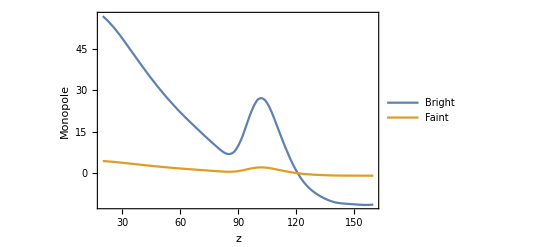

```mathematica
Plot[{d^2MonopoleBf[d],d^2MonopoleFf[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Monopole"},RotateLabel->True, ImageSize->{300},PlotLegends->{Bright, Faint}]
```

## Dipole

```mathematica
g1[z_]:=2/(r[z] HH[z])+1/2(-Omm(1+z)+2/(1+z)^2(1-Omm))/HH[z]^2
```

```mathematica
g1zSKA=Table[g1[i],{i,zSKA}]
```

{15.1422,9.64318,7.20087,5.78564,4.84435,4.16406,3.64492,3.23351,2.89842,2.61978,2.3843,2.18266,2.00812,1.85564,1.72137,1.60229,1.49603,1.40068,1.31468}

```mathematica
DipoleΛCDM=evolzSKA HzSKA(3(smodelBzSKA-smodelFzSKA)fzSKA^2 (1/(rH0zSKA HzSKA)-1)- 5(bBzSKA smodelFzSKA-bFzSKA smodelBzSKA)(1/(rH0zSKA HzSKA)-1) fzSKA+(bBzSKA-bFzSKA) g1zSKA fzSKA)
```

{9.58442,6.45739,4.59397,2.9275,1.82285,1.15263,0.752084,0.482323,0.313696,0.232745,0.213486,0.23159,0.261284,0.294857,0.329052,0.36469,0.403298,0.447018,0.494591}

```mathematica
Dipole=(HzSKA/Sigma8z0^2)(3 (βBzSKA-βFzSKA)GtildezSKA^2/5-(bBtildezSKA βFzSKA-bFtildezSKA βBzSKA)GtildezSKA -(bBtildezSKA-bFtildezSKA)(1-2 /(rH0zSKA  HzSKA))GtildezSKA+(3/2)(bBtildezSKA-bFtildezSKA)IhatzSKA-(bBtildezSKA-bFtildezSKA)dGtildezSKA /(H0 HzSKA))
```

{9.2152,3.04988,1.15167,0.621278,0.709724,0.88793,1.08622,1.36153,1.65069,1.88083,2.00581,2.01926,1.99943,1.97333,1.97407,2.00861,2.08499,2.21087,2.34514}

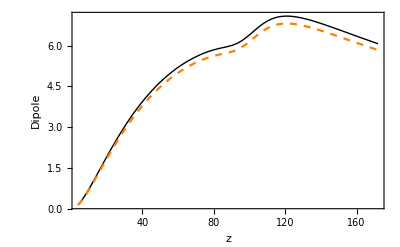

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d],d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

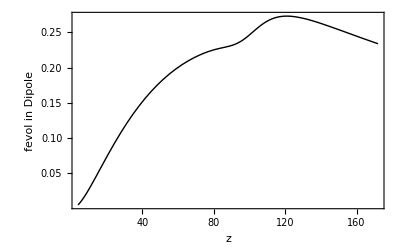

```mathematica
Plot[{d^2DipoleΛCDM[[1]] nu1z0[d]-d^2Dipole[[1]] nu1z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black,Thin},{Orange,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "fevol in Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Dipolez1[d_]:=Dipole[[1]] nu1z0[d]
```

```mathematica
WideAnglezSKA=-(2/5)(bBtildezSKA-bFtildezSKA)GtildezSKA/(rH0zSKA /H0)
```

{-0.000318056,-0.000190554,-0.000134253,-0.000102048,-0.0000810434,-0.0000662349,-0.0000552529,-0.0000468166,-0.0000401661,-0.0000348181,-0.0000304487,-0.0000268317,-0.0000238043,-0.0000212458,-0.0000190655,-0.0000171933,-0.0000155748,-0.0000141671,-0.0000129357}

```mathematica
WideAnglez1[d_]:=WideAnglezSKA[[1]]d mu2z0[d]
```

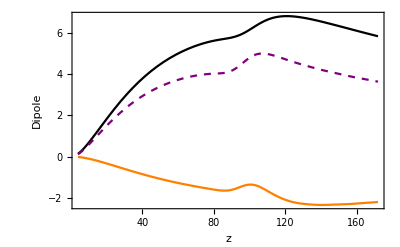

```mathematica
Plot[{d^2Dipole[[1]] nu1z0[d],  d^2(d WideAnglezSKA[[1]] mu2z0[d]),d^2Dipole[[1]] nu1z0[d]+  d^2 (d WideAnglezSKA[[1]] mu2z0[d])},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},PlotStyle->{{Black},{Orange},{Purple,Dashed}}, Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Dipole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Table[Dipolez1[d],{d,4,172,4}]
```

{0.00843408,0.00734428,0.0062338,0.00530906,0.00455647,0.00394215,0.00343621,0.00301545,0.00266223,0.00236309,0.00210772,0.00188818,0.00169821,0.00153287,0.00138814,0.00126077,0.00114814,0.0010479,0.000958225,0.000877632,0.000805076,0.000740945,0.000687363,0.000645885,0.000614566,0.000588283,0.000562118,0.000533883,0.000503797,0.000472916,0.000442279,0.000412734,0.000384803,0.000358656,0.000334324,0.000311834,0.000291146,0.000272107,0.00025455,0.000238382,0.000223528,0.000209864,0.000197245}

```mathematica
Table[WideAnglez1[d],{d,4,172,4}]
```

{-0.000949384,-0.00100454,-0.000961767,-0.000894128,-0.000822202,-0.000752891,-0.000688727,-0.000630224,-0.000577403,-0.000529835,-0.000487023,-0.000448455,-0.000413703,-0.000382304,-0.000354053,-0.000328434,-0.000305385,-0.000284789,-0.000266068,-0.00024907,-0.000232324,-0.000211612,-0.000184306,-0.000155547,-0.000135594,-0.000129731,-0.000133837,-0.000140168,-0.000144155,-0.000144908,-0.000142664,-0.000138038,-0.000132167,-0.000125917,-0.000119386,-0.000112617,-0.00010605,-0.000100015,-0.0000943423,-0.0000887967,-0.000083512,-0.0000787307,-0.0000744011}

```mathematica
Abs[(Table[Dipolez1[d],{d,4,172,4}]-(Table[Dipolez1[d],{d,4,172,4}]+Table[WideAnglez1[d],{d,4,172,4}]))/(Table[Dipolez1[d],{d,4,172,4}])]
```

{0.112565,0.136778,0.154283,0.168415,0.180447,0.190985,0.200432,0.208998,0.216887,0.224213,0.231066,0.237506,0.243611,0.249404,0.255056,0.260503,0.265983,0.27177,0.277667,0.283797,0.288574,0.285598,0.268135,0.240828,0.220634,0.220525,0.238094,0.262545,0.286137,0.306414,0.322565,0.334449,0.343468,0.351081,0.357097,0.361144,0.364251,0.367557,0.370624,0.372498,0.373608,0.375151,0.377202}

```mathematica
rH0zSKA/H0
```

{433.566,704.263,960.18,1201.58,1428.95,1642.94,1844.3,2033.82,2212.29,2380.49,2539.19,2689.08,2830.84,2965.07,3092.35,3213.19,3328.07,3437.42,3541.64}

## Quadrupole

```mathematica
QuadrupoleBright=-(4 bBtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.958985,-0.981859,-0.990866,-0.989223,-0.979907,-0.965463,-0.94794,-0.92892,-0.909575,-0.890749,-0.873026,-0.856796,-0.842311,-0.829717,-0.819095,-0.810474,-0.803855,-0.79922,-0.796541}

```mathematica
QuadrupoleFaint=-(4 bFtildezSKA GtildezSKA/3 + 4 GtildezSKA^2/7)/Sigma8z0^2
```

{-0.266056,-0.307512,-0.343117,-0.373072,-0.397985,-0.418648,-0.435884,-0.450464,-0.463065,-0.474261,-0.484523,-0.494233,-0.5037,-0.513169,-0.522839,-0.53287,-0.543392,-0.554515,-0.566331}

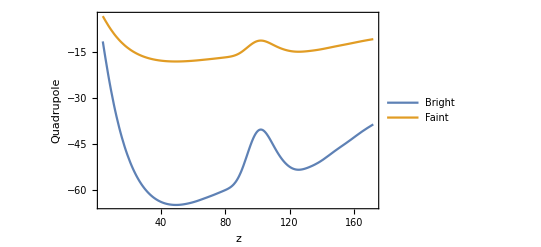

```mathematica
Plot[{d^2 QuadrupoleBright[[1]] mu2z0[d],d^2QuadrupoleFaint [[1]]mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Quadrupole"},RotateLabel->True, ImageSize->{300},PlotLegends-> {Bright,Faint}]
```

```mathematica
QuadrupoleBz1[d_]:=QuadrupoleBright[[1]] mu2z0[d]
QuadrupoleFz1[d_]:=QuadrupoleFaint[[1]] mu2z0[d]
```

## Hexadecapole

```mathematica
Hexadecapole=(8 GtildezSKA^2/35)/Sigma8z0^2
```

{0.0723187,0.0761278,0.0779996,0.0782448,0.0772142,0.0752437,0.0726254,0.0695971,0.0663425,0.0629982,0.0596618,0.0564005,0.053258,0.0502613,0.0474248,0.0447544,0.0422501,0.0399079,0.0377213}

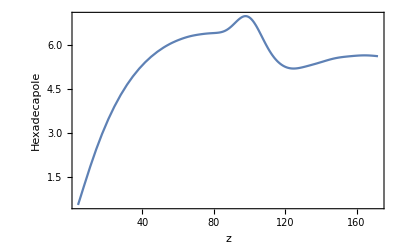

```mathematica
Plot[{d^2Hexadecapole[[1]] mu4z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Hexadecapole"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

```mathematica
Hexadecapolez1[d_]:=Hexadecapole[[1]] mu4z0[d];
```

## Octupole

```mathematica
Octupole=(HzSKA/Sigma8z0^2)2 (βBzSKA-βFzSKA)GtildezSKA^2/5
```

{1.11104,0.280736,0.0377398,0.0040187,0.0553265,0.102001,0.141314,0.191068,0.238223,0.267935,0.274173,0.258214,0.23673,0.21511,0.19876,0.188164,0.183705,0.185598,0.188071}

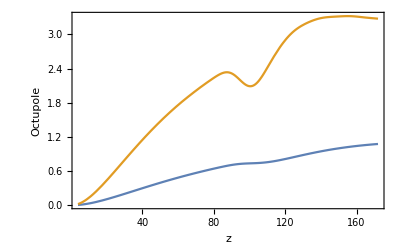

```mathematica
Plot[{d^2 Octupole[[1]] nu3z0[d], d^2 Octupole[[1]] nu3z0[d] - d^2 WideAnglezSKA[[1]]d mu2z0[d]},{d,4,172},PlotRange->{All,All}, Axes->{True,True},AxesOrigin->{0,0},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Octupole"},RotateLabel->True, ImageSize->{300}]
```

```mathematica
Octupolez1[d_]:=Octupole[[1]] nu3z0[d]
OctupoleWAz1[d_]:=Octupole[[1]] nu3z0[d] -WideAnglezSKA[[1]] d mu2z0[d]
```

## Joint plot

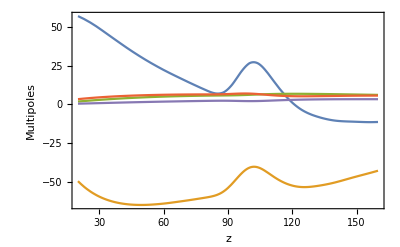

```mathematica
Plot[{d^2 MonopoleBf[d],d^2QuadrupoleBz1[d],d^2Dipolez1[d],d^2Hexadecapolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

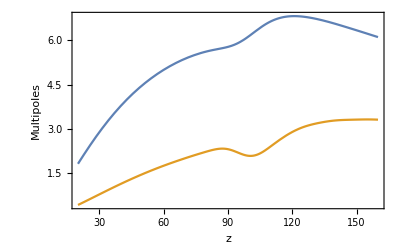

```mathematica
Plot[{d^2Dipolez1[d], d^2 OctupoleWAz1[d]},{d,20,160},PlotRange->{All,All}, Axes->{True,True},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"z",  "Multipoles"},RotateLabel->True, ImageSize->{300},PlotLegends-> None]
```

## Signal-to-noise Ratios

```mathematica
{dmin,dmax}
```

{20,160}

```mathematica
{maxsep,ktot,indist,ldist}
```

{40,19,5,36}

## Monopole

```mathematica
ξ0BSKAmatrix=Table[MonopoleBright[[k]]mu0z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ0BSKAmatrix]
```

{36,19}

```mathematica
Dimensions[varTOTMONOBrightLp4d4to172zSKA]
```

{19,43,43}

```mathematica
varξ0BTOT=Table[ varTOTMONOBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ0BTOT=Table[Inverse[varξ0BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ0BTOT]
```

{19,36,36}

```mathematica
ξ0BSKAmatrix[[All,1]]
```

{0.142339,0.0943027,0.0648831,0.0459406,0.0332482,0.0244804,0.0182718,0.0137867,0.0104874,0.0080278,0.00615659,0.00472639,0.00360615,0.00270355,0.00198465,0.00140355,0.00100613,0.00100434,0.00151842,0.00225057,0.00265239,0.00244426,0.00180944,0.00109687,0.000506807,0.0000757207,-0.000208395,-0.000372615,-0.000463263,-0.0005156,-0.000535955,-0.000528148,-0.000509164,-0.000491792,-0.000472325,-0.000444689}

```mathematica
SNrSKAMonopole=Table[Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{60.6511,94.4015,123.906,149.028,169.713,186.007,197.795,205.004,207.42,204.801,197.394,185.327,169.03,149.638,127.617,104.687,82.2258,61.2833,43.2193}

```mathematica
SNSKAMonopoleTotal= Sqrt[Sum[ξ0BSKAmatrix[[m,k]] invcovξ0BTOT[[k,m,n]] ξ0BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

666.012

## Dipole

```mathematica
ξ1SKAmatrix=Table[(Dipole[[k]])nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{42.9011,23.7382,10.1472,5.20812,5.35035,5.89446,6.22618,6.63539,6.72871,6.30213,5.45379,4.3871,3.4118,2.60465,1.96724,1.4766,1.09965,0.805228,0.565009}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

53.3

```mathematica
1-54.6434/78.2865
```

0.302007

## Dipole + WA

```mathematica
ξ1SKAmatrix=Table[Dipole[[k]]nu1z0[d]+d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ1SKAmatrix]
```

{36,19}

```mathematica
varξ1TOT=Table[varTOTDIP2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ1TOT=Table[Inverse[varξ1TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ1TOT]
```

{19,36,36}

```mathematica
SNrSKADipole=Table[Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{34.8318,14.7025,3.14505,1.60809,1.68347,3.06614,4.15225,5.12809,5.64139,5.52419,4.89958,3.99519,3.13733,2.41402,1.83715,1.38933,1.04241,0.768924,0.542872}

```mathematica
SNSKADipoleTotal= Sqrt[Sum[ξ1SKAmatrix[[m,k]] invcovξ1TOT[[k,m,n]] ξ1SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

40.2856

## Quadrupole

```mathematica
ξ2BSKAmatrix=Table[QuadrupoleBright[[k]]mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ2BSKAmatrix]
```

{36,19}

```mathematica
varξ2BTOT=Table[varTOTQUADBrightLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ2BTOT=Table[Inverse[varξ2BTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ2BTOT]
```

{19,36,36}

```mathematica
ldist
```

36

```mathematica
SNrSKAQuadrupole=Table[Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{42.7304,68.1303,90.6122,109.447,124.226,134.811,141.089,143.098,140.869,134.513,124.595,111.677,96.5811,80.5644,64.3501,49.2233,35.9593,24.9033,16.3321}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ2BSKAmatrix[[m,k]] invcovξ2BTOT[[k,m,n]] ξ2BSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

437.198

## Octupole

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
Octupole[[1;;ktot]]
```

{1.11104,0.280736,0.0377398,0.0040187,0.0553265,0.102001,0.141314,0.191068,0.238223,0.267935,0.274173,0.258214,0.23673,0.21511,0.19876,0.188164,0.183705,0.185598,0.188071}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupole=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{7.01573,2.37137,0.328871,0.0328977,0.406647,0.658923,0.785862,0.899653,0.93257,0.854839,0.701765,0.52033,0.367666,0.252528,0.171266,0.115758,0.0781857,0.0524612,0.0338166}

```mathematica
SNSKAOctupoleTotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

7.71977

```mathematica
1-4.68151/8.50621
```

0.449636

## Octupole + WA

```mathematica
ξ3SKAmatrix=Table[Octupole[[k]]nu1z0[d] -d WideAnglezSKA[[k]] mu2z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ3SKAmatrix]
```

{36,19}

```mathematica
varξ3TOT=Table[varTOTOCT2popLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ3TOT=Table[Inverse[varξ3TOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ3TOT]
```

{19,36,36}

```mathematica
SNrSKAOctupoleWA=Table[Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{19.1398,12.7517,8.00773,5.52964,4.32008,3.46582,2.79964,2.3433,1.96263,1.584,1.21527,0.878635,0.614509,0.420577,0.283143,0.188639,0.124419,0.0807283,0.0504173}

```mathematica
SNSKAOctupoleWATotal= Sqrt[Sum[ξ3SKAmatrix[[m,k]] invcovξ3TOT[[k,m,n]] ξ3SKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

26.0182

## Hexadecapole

```mathematica
ξ4TSKAmatrix=Table[Hexadecapole[[k]]mu4z0[d],{d,dmin,dmax,4},{k,1,ktot}];
Dimensions[ξ4TSKAmatrix]
```

{36,19}

```mathematica
varξ4TTOT=Table[varTOTHEXAtotpopLp4d4to172zSKA[[k,l,m]],{k,1,ktot},{l,indist,maxsep},{m,indist,maxsep}];
```

```mathematica
invcovξ4TTOT=Table[Inverse[varξ4TTOT[[k,All,All]]],{k,1,ktot}];
Dimensions[invcovξ4TTOT]
```

{19,36,36}

```mathematica
SNrSKAHexadecapole=Table[Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]],{m,1,ldist}, {n,1,ldist}]],{k,1,ktot}]
```

{9.7378,15.1786,19.6006,22.8466,24.8844,25.783,25.6376,24.5914,22.7903,20.396,17.6385,14.7113,11.8091,9.1342,6.76497,4.8075,3.27383,2.12239,1.3088}

```mathematica
SNSKAQuadrupoleTotal= Sqrt[Sum[ξ4TSKAmatrix[[m,k]] invcovξ4TTOT[[k,m,n]] ξ4TSKAmatrix[[n,k]], {m,1,ldist}, {n,1,ldist}, {k,1,ktot}]]
```

74.4918

## Plot

```mathematica
SNSKAz015Dipole=Table[ξ1SKAmatrix[[m,1]]/Sqrt[varξ1TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Monopole=Table[ξ0BSKAmatrix[[m,1]]/Sqrt[varξ0BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Quadrupole=Table[Abs[ξ2BSKAmatrix[[m,1]]]/Sqrt[varξ2BTOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Octupole=Table[Abs[ξ3SKAmatrix[[m,1]]]/Sqrt[varξ3TOT[[1,m,m]]],{m,1,ldist}];
SNSKAz015Hexadecapole=Table[Abs[ξ4TSKAmatrix[[m,1]]]/Sqrt[varξ4TTOT[[1,m,m]]],{m,1,ldist}];
```

```mathematica
ds=Table[d,{d,dmin,dmax,4}];
```

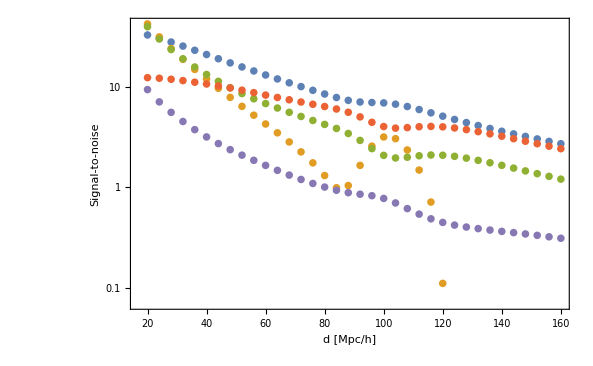

```mathematica
ListLogPlot[{Table[{ds[[i]], SNSKAz015Dipole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Monopole[[i]]},{i,1,ldist}],Table[{ds[[i]], SNSKAz015Quadrupole[[i]]},{i,1,ldist}], Table[{ds[[i]], SNSKAz015Octupole[[i]]},{i,1,ldist}],
Table[{ds[[i]], SNSKAz015Hexadecapole[[i]]},{i,1,ldist}]},PlotRange->Full,PlotStyle->{•},Axes->{False,False},Frame->True,FrameStyle->Directive[Black],LabelStyle->Directive[Black, 12],FrameLabel->{"d [Mpc/h]","Signal-to-noise"},RotateLabel->True]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["multi_split"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/multi_split

```mathematica
(*Export["CovarianceMatrixzSKA_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA,"Table","FieldSeparators"->" ",OverwriteTarget->"KeepBoth"]*)
```

```mathematica
(*Export["CovarianceMatrix_P_at_z"<>ToString[zSKA[[1]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>".txt",CovMatrixtabzSKA[[1]],"Table","FieldSeparators"->" ",OverwriteTarget->True]*)
```

```mathematica
nBSKA
```

1/2

```mathematica
nFSKA
```

1/2

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrix_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

EXPORT - WITH OCTUPOLE

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance

```mathematica
SetDirectory["octupole"]
```

/Users/danielsb/Documents/GitHub/magevolbias/Covariance/octupole

```mathematica
For[i=1,i<= Length[zSKA],i++,
Export["CovarianceMatrixOCT_at_z"<>ToString[zSKA[[i]]]<>"_d"<>ToString[distances[[indist]]]<>"to"<>ToString[distances[[maxsep]]]<>"_msplit-"<>StringReplace[ToString[Round[100 N[nBSKA]], InputForm],"/"->"-"]<>"B_"<>StringReplace[ToString[Round[100N[nFSKA]], InputForm],"/"->"-"]<>"F.txt",CovMatrixOCTtabzSKA[[i]],"Table","FieldSeparators"->" ",OverwriteTarget->True]]
```

```mathematica
nBSKA
```

1/2

```mathematica
nFSKA
```

1/2

```mathematica
Exit[]
```